```mathematica
Manipulate[
Show[
ContourPlot[Abs[x]^(n)+Abs[y]^(n)==1,{x,-1.6,1.6},{y,-1.6,1.6}],
ParametricPlot[{1,x},{x,-1,1},PlotStyle->Red],ParametricPlot[{-1,x},{x,-1,1},PlotStyle->Red],
ParametricPlot[{x,1},{x,-1,1},PlotStyle->Red],ParametricPlot[{x,-1},{x,-1,1},PlotStyle->Red]
]
,{n,2,50}
]
```

```mathematica
Integrate[r/r7 Log[r/r8],r]
```

(-r^2/4+1/2 r^2 Log[r/r8])/r7

```mathematica
Integrate[r/2/r7 Log[r/r8]-r/4/r7+r9/r,r]
```

-r^2/(4 r7)+r9 Log[r]+(r^2 Log[r/r8])/(4 r7)

```mathematica
D[r2 Log[r/r3]+r^2/4/r4(1+λ Log[r/r5]),r]
```

r2/r+(r λ)/(4 r4)+(r (1+λ Log[r/r5]))/(2 r4)

```mathematica
FullSimplify[1/r D[r D[1/r D[r D[ψ[r],r],r],r],r]]
```

(ψ'[r]-r ψ''[r]+2 r^2 ψ^(3)[r])/r^3+ψ^(4)[r]

```mathematica
FullSimplify[λ(λ-1)(λ-2)(λ-3)+2λ(λ-1)(λ-2)-(1+2m^2)λ(λ-1)+(1-2m^2)λ+(m^4-4m^2)]
```

m^4+(-2+λ)^2 λ^2-2 m^2 (2+λ^2)

```mathematica
Discriminant[a x^2 +b x+c,x]
```

b^2-4 a c

```mathematica
Discriminant[a x^4 +b x^3+c x^2+d x+e,x]
```

b^2 c^2 d^2-4 a c^3 d^2-4 b^3 d^3+18 a b c d^3-27 a^2 d^4-4 b^2 c^3 e+16 a c^4 e+18 b^3 c d e-80 a b c^2 d e-6 a b^2 d^2 e+144 a^2 c d^2 e-27 b^4 e^2+144 a b^2 c e^2-128 a^2 c^2 e^2-192 a^2 b d e^2+256 a^3 e^3

```mathematica
Discriminant[m^4+(-2+λ)^2 λ^2-2 m^2 (2+λ^2),λ]
```

-256 (-4 m^2+m^4) (12 m^2-69 m^4+16 m^6)

```mathematica
Discriminant[(12-69 m+16 m^2),m]
```

3993

```mathematica
N[Solve[12-69 m^2+16 m^4==0,m]]
```

{{m→-0.426095},{m→0.426095},{m→-2.03247},{m→2.03247}}

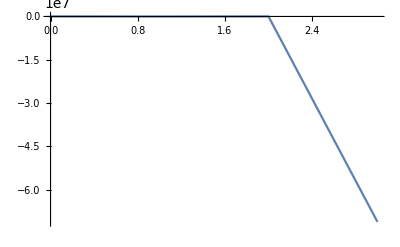

```mathematica
ListLinePlot[Table[{m,-256 (-4 m^2+m^4) (12 m^2-69 m^4+16 m^6)},{m,0,3}]]
```

```mathematica
(-256 (-4 m^2+m^4) (12 m^2-69 m^4+16 m^6))/.{m->1}
```

-31488

```mathematica
(-256 (-4 m^2+m^4) (12 m^2-69 m^4+16 m^6))/.{m->2}
```

0

```mathematica
(-256 (-4 m^2+m^4) (12 m^2-69 m^4+16 m^6))/.{m->3}
```

-71228160

```mathematica
Manipulate[N[Solve[m^4+(-2+λ)^2 λ^2-2 m^2 (2+λ^2)==0,λ]],{m,3,9,1}]
```

```mathematica
Solve[(x-1)(x-2)(x-3)+2(x-1)(x-2)-9(x-1)-7==0,x]
```

{{x→0},{x→2 (1-√2)},{x→2 (1+√2)}}

```mathematica
DSolve[D[Rm[r],{r,4}]+2/r D[Rm[r],{r,3}]-9/r^2 D[Rm[r],{r,2}]-7/r^3 D[Rm[r],r]==0,Rm[r],r]
```

{{Rm[r]→(r^(2-2 √2) C[1])/(2-2 √2)+(r^(2+2 √2) C[2])/(2+2 √2)+C[4]+C[3] Log[r]}}

```mathematica
DSolve[D[Rm[r],{r,4}]+2/r D[Rm[r],{r,3}]-1/r^2 D[Rm[r],{r,2}]+1/r^3 D[Rm[r],r]==0,Rm[r],r]
```

{{Rm[r]→1/2 r^2 C[2]-1/4 r^2 C[3]+C[4]+C[1] Log[r]+1/2 r^2 C[3] Log[r]}}

```mathematica
D[r^2(A[3]+A[4]Log[r/r2]),r]
```

r A[4]+2 r (A[3]+A[4] Log[r/r2])

```mathematica
Limit[x Log[x],x->0]
```

0

```mathematica
Limit[x Log[1/x],x->0]
```

0

```mathematica
D[(x^n+y^n)^(1/n),x]
```

x^(-1+n) (x^n+y^n)^(-1+1/n)

```mathematica
D[(x^n+y^n)^(1/n),y]
```

y^(-1+n) (x^n+y^n)^(-1+1/n)

```mathematica
FullSimplify[D[ArcTan[(y/x)^(n/2)],x]]
```

-(n (y/x)^(n/2))/(2 x+2 x (y/x)^n)

```mathematica
FullSimplify[D[ArcTan[(y/x)^(n/2)],y]]
```

(n (y/x)^(n/2))/(2 y+2 y (y/x)^n)

```mathematica
D[Cos[θ]^(2/n),θ]
```

-(2 Cos[θ]^(-1+2/n) Sin[θ])/n

```mathematica
D[Sin[θ]^(2/n),θ]
```

(2 Cos[θ] Sin[θ]^(-1+2/n))/n

```mathematica
D[Cos[θ]^(2(1-1/n)),θ]
```

-2 (1-1/n) Cos[θ]^(-1+2 (1-1/n)) Sin[θ]

```mathematica
FullSimplify[n^2/16/r^2D[Sin[2 θ]/(Cos[θ])^(2/n)f'[θ],θ]]
```

(n Cos[θ]^(-(2+n)/n) (2 (n Cos[θ] Cos[2 θ]+Sin[θ] Sin[2 θ]) f'[θ]+n Cos[θ] Sin[2 θ] f''[θ]))/(16 r^2)

```mathematica
Block[
{x,y,n,r,θ},
r[x_,y_]:=x^n+y^n;
θ[x_,y_]:=ArcTan[(y/x)^(n/2)];
D[f[r,θ]]
]
```

f[r,θ]

```mathematica
Block[
{x,y,n,r,θ,f,dfx,dfy,dfx2,dfx3,dfx4,dfy2,dfy3,dfx2y,dfx2y2,dfy4},
x[r_,θ_]:=r Cos[θ]^(2/n);
y[r_,θ_]:=r Sin[θ]^(2/n);
dfx[r_,θ_]:=D[f[r,θ],r]/D[x[r,θ],r]+D[f[r,θ],θ]/D[x[r,θ],θ];
dfy[r_,θ_]:=D[f[r,θ],r]/D[y[r,θ],r]+D[f[r,θ],θ]/D[y[r,θ],θ];
dfx2[r_,θ_]:=D[dfx[r,θ],r]/D[x[r,θ],r]+D[dfx[r,θ],θ]/D[x[r,θ],θ];
dfy2[r_,θ_]:=D[dfy[r,θ],r]/D[y[r,θ],r]+D[dfy[r,θ],θ]/D[y[r,θ],θ];
dfx3[r_,θ_]:=D[dfx2[r,θ],r]/D[x[r,θ],r]+D[dfx2[r,θ],θ]/D[x[r,θ],θ];
dfy3[r_,θ_]:=D[dfy2[r,θ],r]/D[y[r,θ],r]+D[dfy2[r,θ],θ]/D[y[r,θ],θ];
dfx2y[r_,θ_]:=D[dfx2[r,θ],r]/D[y[r,θ],r]+D[dfx2[r,θ],θ]/D[y[r,θ],θ];
dfx4[r_,θ_]:=D[dfx3[r,θ],r]/D[x[r,θ],r]+D[dfx3[r,θ],θ]/D[x[r,θ],θ];
dfy4[r_,θ_]:=D[dfy3[r,θ],r]/D[y[r,θ],r]+D[dfy3[r,θ],θ]/D[y[r,θ],θ];
dfx2y2[r_,θ_]:=D[dfx2y[r,θ],r]/D[y[r,θ],r]+D[dfx2y[r,θ],θ]/D[y[r,θ],θ];
Print["∂f/∂x = ",Collect[D[f[r,θ],r]/D[x[r,θ],r]+D[f[r,θ],θ]/D[x[r,θ],θ],{D[f[r,θ],r],D[f[r,θ],θ]},FullSimplify]];
Print["∂f/∂y = ",Collect[D[f[r,θ],r]/D[y[r,θ],r]+D[f[r,θ],θ]/D[y[r,θ],θ],{D[f[r,θ],r],D[f[r,θ],θ]},FullSimplify]];
Print["∂2f/∂x2 = ",Collect[D[dfx[r,θ],r]/D[x[r,θ],r]+D[dfx[r,θ],θ]/D[x[r,θ],θ],{D[f[r,θ],r],D[f[r,θ],θ],D[f[r,θ],{r,θ}],D[f[r,θ],{r,r}],D[f[r,θ],{θ,θ}]}]];
Print["∂2f/∂y2 = ",Collect[D[dfy[r,θ],r]/D[y[r,θ],r]+D[dfy[r,θ],θ]/D[y[r,θ],θ],{D[f[r,θ],r],D[f[r,θ],θ],D[f[r,θ],{r,θ}],D[f[r,θ],{r,r}],D[f[r,θ],{θ,θ}]}]];
Print["∂4f/∂x4 = ",Collect[D[dfx3[r,θ],r]/D[x[r,θ],r]+D[dfx3[r,θ],θ]/D[x[r,θ],θ],{D[f[r,θ],r],D[f[r,θ],θ],D[f[r,θ],{r,θ}],D[f[r,θ],{r,r}],D[f[r,θ],{θ,θ}],D[f[r,θ],{r,3}],D[f[r,θ],{r,2},{θ,1}],D[f[r,θ],{r,1},{θ,2}],D[f[r,θ],{θ,3}],D[f[r,θ],{r,4}],D[f[r,θ],{r,3},{θ,1}],D[f[r,θ],{r,2},{θ,2}],D[f[r,θ],{r,1},{θ,3}],D[f[r,θ],{θ,4}]},FullSimplify]];
Print["∂4f/∂y4 = ",Collect[D[dfy3[r,θ],r]/D[y[r,θ],r]+D[dfy3[r,θ],θ]/D[y[r,θ],θ],{D[f[r,θ],r],D[f[r,θ],θ],D[f[r,θ],{r,θ}],D[f[r,θ],{r,r}],D[f[r,θ],{θ,θ}],D[f[r,θ],{r,3}],D[f[r,θ],{r,2},{θ,1}],D[f[r,θ],{r,1},{θ,2}],D[f[r,θ],{θ,3}],D[f[r,θ],{r,4}],D[f[r,θ],{r,3},{θ,1}],D[f[r,θ],{r,2},{θ,2}],D[f[r,θ],{r,1},{θ,3}],D[f[r,θ],{θ,4}]},FullSimplify]];
Collect[dfx4[r,θ]+dfy4[r,θ]+2 dfx2y2[r,θ],{D[f[r,θ],r],D[f[r,θ],θ],D[f[r,θ],{r,θ}],D[f[r,θ],{r,r}],D[f[r,θ],{θ,θ}],D[f[r,θ],{r,3}],D[f[r,θ],{r,2},{θ,1}],D[f[r,θ],{r,1},{θ,2}],D[f[r,θ],{θ,3}],D[f[r,θ],{r,4}],D[f[r,θ],{r,3},{θ,1}],D[f[r,θ],{r,2},{θ,2}],D[f[r,θ],{r,1},{θ,3}],D[f[r,θ],{θ,4}]},FullSimplify]
]
```

∂f/∂x = -(n Cos[θ]^((-2+n)/n) Csc[θ] f^(0,1)[r,θ])/(2 r)+Cos[θ]^(-2/n) f^(1,0)[r,θ]

∂f/∂y = (n Csc[2 θ] Sin[θ]^(2-2/n) f^(0,1)[r,θ])/r+Sin[θ]^(-2/n) f^(1,0)[r,θ]

∂2f/∂x2 = ((n Cos[θ]^(1-4/n) Csc[θ])/(2 r^2)+((-1+2/n) n^2 Cos[θ]^(1-4/n) Csc[θ])/(4 r^2)-(n^2 Cos[θ]^(3-4/n) Csc[θ]^3)/(4 r^2)) f^(0,1)[r,θ]+(n^2 Cos[θ]^(2-4/n) Csc[θ]^2 f^(0,2)[r,θ])/(4 r^2)-(Cos[θ]^(-4/n) f^(1,0)[r,θ])/r-(n Cos[θ]^(1-4/n) Csc[θ] f^(1,1)[r,θ])/r+Cos[θ]^(-4/n) f^(2,0)[r,θ]

∂2f/∂y2 = (-(n Sec[θ] Sin[θ]^(1-4/n))/(2 r^2)+((1-2/n) n^2 Sec[θ] Sin[θ]^(1-4/n))/(4 r^2)+(n^2 Sec[θ]^3 Sin[θ]^(3-4/n))/(4 r^2)) f^(0,1)[r,θ]+(n^2 Sec[θ]^2 Sin[θ]^(2-4/n) f^(0,2)[r,θ])/(4 r^2)-(Sin[θ]^(-4/n) f^(1,0)[r,θ])/r+(n Sec[θ] Sin[θ]^(1-4/n) f^(1,1)[r,θ])/r+Sin[θ]^(-4/n) f^(2,0)[r,θ]

∂4f/∂x4 = -(n Cos[θ]^((-8+n)/n) Csc[θ] (-384+n Csc[θ]^2 (176+4 n (12+n)-18 n (4+n) Csc[θ]^2+15 n^2 Csc[θ]^4)) f^(0,1)[r,θ])/(16 r^4)-(3 n^3 Cos[θ]^(3-8/n) (-2+n+2 Cos[2 θ]) Csc[θ]^5 f^(0,3)[r,θ])/(8 r^4)+(n^4 Cos[θ]^(4-8/n) Csc[θ]^4 f^(0,4)[r,θ])/(16 r^4)-(15 Cos[θ]^(-8/n) f^(1,0)[r,θ])/r^3+(3 n^2 Cos[θ]^(2-8/n) Csc[θ]^2 (-5+n Csc[θ]^2) f^(1,2)[r,θ])/(2 r^3)-(n^3 Cos[θ]^(3-8/n) Csc[θ]^3 f^(1,3)[r,θ])/(2 r^3)+1/(16 r^4)Cos[θ]^(-8/n) (n^2 (66+n (-36+11 n)+4 (-2+n) (11+n) Cos[2 θ]+22 Cos[4 θ]) Cot[θ]^2 Csc[θ]^4 f^(0,2)[r,θ]+8 r (n Cot[θ] (-56+n Csc[θ]^2 (15+2 n-3 n Csc[θ]^2)) f^(1,1)[r,θ]+30 r f^(2,0)[r,θ]))-(3 n Cos[θ]^((-8+n)/n) Csc[θ] (-8+n Csc[θ]^2) f^(2,1)[r,θ])/(2 r^2)+(3 n^2 Cos[θ]^(2-8/n) Csc[θ]^2 f^(2,2)[r,θ])/(2 r^2)-(6 Cos[θ]^(-8/n) f^(3,0)[r,θ])/r-(2 n Cos[θ]^((-8+n)/n) Csc[θ] f^(3,1)[r,θ])/r+Cos[θ]^(-8/n) f^(4,0)[r,θ]

∂4f/∂y4 = (n Sec[θ] (-384+n Sec[θ]^2 (176+4 n (12+n)-18 n (4+n) Sec[θ]^2+15 n^2 Sec[θ]^4)) Sin[θ]^((-8+n)/n) f^(0,1)[r,θ])/(16 r^4)+(3 n^3 Sec[θ]^3 (-4+n Sec[θ]^2) Sin[θ]^(3-8/n) f^(0,3)[r,θ])/(8 r^4)+(n^4 Csc[2 θ]^4 Sin[θ]^(8-8/n) f^(0,4)[r,θ])/r^4-(15 Sin[θ]^(-8/n) f^(1,0)[r,θ])/r^3+(3 n^2 Sec[θ]^2 (-5+n Sec[θ]^2) Sin[θ]^(2-8/n) f^(1,2)[r,θ])/(2 r^3)+(n^3 Sec[θ]^3 Sin[θ]^(3-8/n) f^(1,3)[r,θ])/(2 r^3)+1/(16 r^4)Sin[θ]^(-8/n) (n^2 (66+n (-36+11 n)-4 (-2+n) (11+n) Cos[2 θ]+22 Cos[4 θ]) Sec[θ]^4 Tan[θ]^2 f^(0,2)[r,θ]+8 r (n (56+n Sec[θ]^2 (-15-2 n+3 n Sec[θ]^2)) Tan[θ] f^(1,1)[r,θ]+30 r f^(2,0)[r,θ]))+(3 n Sec[θ] (-8+n Sec[θ]^2) Sin[θ]^((-8+n)/n) f^(2,1)[r,θ])/(2 r^2)+(3 n^2 Sec[θ]^2 Sin[θ]^(2-8/n) f^(2,2)[r,θ])/(2 r^2)-(6 Sin[θ]^(-8/n) f^(3,0)[r,θ])/r+(2 n Sec[θ] Sin[θ]^((-8+n)/n) f^(3,1)[r,θ])/r+Sin[θ]^(-8/n) f^(4,0)[r,θ]

-1/(16 r^4)n Cos[θ]^(-7-8/n) Sin[θ]^(-7-8/n) (-(-12+n) (-8+n) (-4+n) Cos[θ]^(6+8/n) Sin[θ]^8-(-4+n) n (-44+13 n) Cos[θ]^(4+8/n) Sin[θ]^10-9 n^2 (-8+3 n) Cos[θ]^(2+8/n) Sin[θ]^12-15 n^3 Cos[θ]^(8/n) Sin[θ]^14+2 n (4+3 n) (8+3 n) Cos[θ]^(10+4/n) Sin[θ]^(4+4/n)+2 (-128+n (-64+n (28+13 n))) Cos[θ]^(8+4/n) Sin[θ]^(6+4/n)+2 (-4+n) (-48+n (8+3 n)) Cos[θ]^(6+4/n) Sin[θ]^(8+4/n)-2 (-4+n)^2 (4+n) Cos[θ]^(4+4/n) Sin[θ]^(10+4/n)+9 n^2 (-8+3 n) Cos[θ]^12 Sin[θ]^(2+8/n)+(-4+n) n (-44+13 n) Cos[θ]^10 Sin[θ]^(4+8/n)+(-12+n) (-8+n) (-4+n) Cos[θ]^8 Sin[θ]^(6+8/n)+15 n^3 Cos[θ]^14 Sin[θ]^(8/n)) f^(0,1)[r,θ]+1/(8 r^4)n^3 Cos[θ]^(-5-8/n) Sin[θ]^(-5-8/n) (3 Cos[θ]^(8/n) (-2+n-2 Cos[2 θ]) Sin[θ]^8-4 Cos[θ]^(4+4/n) (n+3 Cos[2 θ]) Sin[θ]^(4+4/n)-3 Cos[θ]^8 (-2+n+2 Cos[2 θ]) Sin[θ]^(8/n)) f^(0,3)[r,θ]+(n^4 Cos[θ]^(-(4 (2+n))/n) Sin[θ]^(4-8/n) (Cos[θ]^(4/n)+Cos[θ]^4 Sin[θ]^(-4+4/n))^2 f^(0,4)[r,θ])/(16 r^4)+((-60 Cos[θ]^(-8/n)-60 Sin[θ]^(-8/n)+Cos[θ]^(-(4 (1+n))/n) (-13-8 n+(4+8 n) Cos[2 θ]-15 Cos[4 θ]) Sin[θ]^(-4/n)) f^(1,0)[r,θ])/(4 r^3)+1/(8 r^3)n^2 Cos[θ]^(-(4 (2+n))/n) Sin[θ]^(-(4 (2+n))/n) (-6 Cos[θ]^(8/n) (5-2 n+5 Cos[2 θ]) Sin[θ]^6-Cos[θ]^(2+4/n) (13+4 n+8 (-1+n) Cos[2 θ]+15 Cos[4 θ]) Sin[θ]^(2+4/n)+6 Cos[θ]^6 (-5+2 n+5 Cos[2 θ]) Sin[θ]^(8/n)) f^(1,2)[r,θ]+(n^3 Cos[θ]^(-3-8/n) (-Cos[θ]^3 Cot[θ]^3+Cos[θ]^(8/n) Sin[θ]^(3-8/n)+Cos[θ]^(2+4/n) Cos[2 θ] Sin[θ]^(-(4+n)/n)) f^(1,3)[r,θ])/(2 r^3)+1/(16 r^4)Cos[θ]^(-6-8/n) Sin[θ]^(-6-8/n) (n^2 (Cos[θ]^(8/n) (66+n (-36+11 n)-4 (-2+n) (11+n) Cos[2 θ]+22 Cos[4 θ]) Sin[θ]^8+2 Cos[θ]^(4+4/n) (18+n (8+5 n)+4 (-2+n (7+n)) Cos[2 θ]+22 Cos[4 θ]) Sin[θ]^(4+4/n)+Cos[θ]^8 (66+n (-36+11 n)+4 (-2+n) (11+n) Cos[2 θ]+22 Cos[4 θ]) Sin[θ]^(8/n)) f^(0,2)[r,θ]+4 r Cos[θ] Sin[θ] (n (Cos[θ]^(8/n) (42+n (-15+4 n)+(56-n (15+2 n)) Cos[2 θ]+14 Cos[4 θ]) Sin[θ]^6+Cos[θ]^(2+4/n) (-12+n (-1+3 n)+(17+2 n (3+n)) Cos[2 θ]+(-12+n (5+n)) Cos[4 θ]+7 Cos[6 θ]) Sin[θ]^(2+4/n)-Cos[θ]^6 (42+n (-15+4 n)+(-56+n (15+2 n)) Cos[2 θ]+14 Cos[4 θ]) Sin[θ]^(8/n)) f^(1,1)[r,θ]+r Cos[θ] Sin[θ]^5 (60 Cos[θ]^(4+8/n)+Cos[θ]^(4/n) (13+8 n-4 (1+2 n) Cos[2 θ]+15 Cos[4 θ]) Sin[θ]^(4/n)+60 Cos[θ]^4 Sin[θ]^(8/n)) f^(2,0)[r,θ]))+1/(4 r^2)n Sec[θ]^2 (-6 Cos[θ]^(4-8/n) (-4+n+4 Cos[2 θ]) Csc[θ]^4+6 (-4+n-4 Cos[2 θ]) Sin[θ]^(-8/n)+Cos[θ]^(-4/n) (4+n-(5+2 n) Cos[2 θ]-(-4+n) Cos[4 θ]-3 Cos[6 θ]) Sin[θ]^(-(4 (1+n))/n)) Tan[θ] f^(2,1)[r,θ]+(n^2 Cos[θ]^(-(2 (4+n))/n) Sin[θ]^(-(2 (4+n))/n) (12 Cos[θ]^(8/n) Sin[θ]^4+Cos[θ]^(4/n) (1+3 Cos[4 θ]) Sin[θ]^(4/n)+12 Cos[θ]^4 Sin[θ]^(8/n)) f^(2,2)[r,θ])/(8 r^2)+(2 (-3 Cos[θ]^(-8/n)-3 Sin[θ]^(-8/n)+Cos[θ]^(-(2 (2+n))/n) (1-3 Cos[2 θ]) Sin[θ]^(-4/n)) f^(3,0)[r,θ])/r+(2 n Cos[θ]^(-(8+n)/n) Sin[θ]^((-8+n)/n) (Cos[θ]^(4/n)-Cos[θ]^2 Sin[θ]^(-2+4/n)) (Cos[θ]^(4/n)+Sin[θ]^(4/n)) f^(3,1)[r,θ])/r+Cos[θ]^(-8/n) Sin[θ]^(-8/n) (Cos[θ]^(4/n)+Sin[θ]^(4/n))^2 f^(4,0)[r,θ]

```mathematica
Block[
{f,n,r,θ,bilap},
bilap[r_,θ_]:=-1/(16 r^4)n Cos[θ]^(-7-8/n) Sin[θ]^(-7-8/n) (-(-12+n) (-8+n) (-4+n) Cos[θ]^(6+8/n) Sin[θ]^8-(-4+n) n (-44+13 n) Cos[θ]^(4+8/n) Sin[θ]^10-9 n^2 (-8+3 n) Cos[θ]^(2+8/n) Sin[θ]^12-15 n^3 Cos[θ]^(8/n) Sin[θ]^14+2 n (4+3 n) (8+3 n) Cos[θ]^(10+4/n) Sin[θ]^(4+4/n)+2 (-128+n (-64+n (28+13 n))) Cos[θ]^(8+4/n) Sin[θ]^(6+4/n)+2 (-4+n) (-48+n (8+3 n)) Cos[θ]^(6+4/n) Sin[θ]^(8+4/n)-2 (-4+n)^2 (4+n) Cos[θ]^(4+4/n) Sin[θ]^(10+4/n)+9 n^2 (-8+3 n) Cos[θ]^12 Sin[θ]^(2+8/n)+(-4+n) n (-44+13 n) Cos[θ]^10 Sin[θ]^(4+8/n)+(-12+n) (-8+n) (-4+n) Cos[θ]^8 Sin[θ]^(6+8/n)+15 n^3 Cos[θ]^14 Sin[θ]^(8/n)) Derivative[0,1][f][r,θ]+1/(8 r^4)n^3 Cos[θ]^(-5-8/n) Sin[θ]^(-5-8/n) (3 Cos[θ]^(8/n) (-2+n-2 Cos[2 θ]) Sin[θ]^8-4 Cos[θ]^(4+4/n) (n+3 Cos[2 θ]) Sin[θ]^(4+4/n)-3 Cos[θ]^8 (-2+n+2 Cos[2 θ]) Sin[θ]^(8/n)) Derivative[0,3][f][r,θ]+(n^4 Cos[θ]^(-(4 (2+n))/n) Sin[θ]^(4-8/n) (Cos[θ]^(4/n)+Cos[θ]^4 Sin[θ]^(-4+4/n))^2 Derivative[0,4][f][r,θ])/(16 r^4)+((-60 Cos[θ]^(-8/n)-60 Sin[θ]^(-8/n)+Cos[θ]^(-(4 (1+n))/n) (-13-8 n+(4+8 n) Cos[2 θ]-15 Cos[4 θ]) Sin[θ]^(-4/n)) Derivative[1,0][f][r,θ])/(4 r^3)+1/(8 r^3)n^2 Cos[θ]^(-(4 (2+n))/n) Sin[θ]^(-(4 (2+n))/n) (-6 Cos[θ]^(8/n) (5-2 n+5 Cos[2 θ]) Sin[θ]^6-Cos[θ]^(2+4/n) (13+4 n+8 (-1+n) Cos[2 θ]+15 Cos[4 θ]) Sin[θ]^(2+4/n)+6 Cos[θ]^6 (-5+2 n+5 Cos[2 θ]) Sin[θ]^(8/n)) Derivative[1,2][f][r,θ]+(n^3 Cos[θ]^(-3-8/n) (-Cos[θ]^3 Cot[θ]^3+Cos[θ]^(8/n) Sin[θ]^(3-8/n)+Cos[θ]^(2+4/n) Cos[2 θ] Sin[θ]^(-(4+n)/n)) Derivative[1,3][f][r,θ])/(2 r^3)+1/(16 r^4)Cos[θ]^(-6-8/n) Sin[θ]^(-6-8/n) (n^2 (Cos[θ]^(8/n) (66+n (-36+11 n)-4 (-2+n) (11+n) Cos[2 θ]+22 Cos[4 θ]) Sin[θ]^8+2 Cos[θ]^(4+4/n) (18+n (8+5 n)+4 (-2+n (7+n)) Cos[2 θ]+22 Cos[4 θ]) Sin[θ]^(4+4/n)+Cos[θ]^8 (66+n (-36+11 n)+4 (-2+n) (11+n) Cos[2 θ]+22 Cos[4 θ]) Sin[θ]^(8/n)) Derivative[0,2][f][r,θ]+4 r Cos[θ] Sin[θ] (n (Cos[θ]^(8/n) (42+n (-15+4 n)+(56-n (15+2 n)) Cos[2 θ]+14 Cos[4 θ]) Sin[θ]^6+Cos[θ]^(2+4/n) (-12+n (-1+3 n)+(17+2 n (3+n)) Cos[2 θ]+(-12+n (5+n)) Cos[4 θ]+7 Cos[6 θ]) Sin[θ]^(2+4/n)-Cos[θ]^6 (42+n (-15+4 n)+(-56+n (15+2 n)) Cos[2 θ]+14 Cos[4 θ]) Sin[θ]^(8/n)) Derivative[1,1][f][r,θ]+r Cos[θ] Sin[θ]^5 (60 Cos[θ]^(4+8/n)+Cos[θ]^(4/n) (13+8 n-4 (1+2 n) Cos[2 θ]+15 Cos[4 θ]) Sin[θ]^(4/n)+60 Cos[θ]^4 Sin[θ]^(8/n)) Derivative[2,0][f][r,θ]))+1/(4 r^2)n Sec[θ]^2 (-6 Cos[θ]^(4-8/n) (-4+n+4 Cos[2 θ]) Csc[θ]^4+6 (-4+n-4 Cos[2 θ]) Sin[θ]^(-8/n)+Cos[θ]^(-4/n) (4+n-(5+2 n) Cos[2 θ]-(-4+n) Cos[4 θ]-3 Cos[6 θ]) Sin[θ]^(-(4 (1+n))/n)) Tan[θ] Derivative[2,1][f][r,θ]+(n^2 Cos[θ]^(-(2 (4+n))/n) Sin[θ]^(-(2 (4+n))/n) (12 Cos[θ]^(8/n) Sin[θ]^4+Cos[θ]^(4/n) (1+3 Cos[4 θ]) Sin[θ]^(4/n)+12 Cos[θ]^4 Sin[θ]^(8/n)) Derivative[2,2][f][r,θ])/(8 r^2)+(2 (-3 Cos[θ]^(-8/n)-3 Sin[θ]^(-8/n)+Cos[θ]^(-(2 (2+n))/n) (1-3 Cos[2 θ]) Sin[θ]^(-4/n)) Derivative[3,0][f][r,θ])/r+(2 n Cos[θ]^(-(8+n)/n) Sin[θ]^((-8+n)/n) (Cos[θ]^(4/n)-Cos[θ]^2 Sin[θ]^(-2+4/n)) (Cos[θ]^(4/n)+Sin[θ]^(4/n)) Derivative[3,1][f][r,θ])/r+Cos[θ]^(-8/n) Sin[θ]^(-8/n) (Cos[θ]^(4/n)+Sin[θ]^(4/n))^2 Derivative[4,0][f][r,θ];
Print[FullSimplify[Coefficient[bilap[r,θ],D[f[r,θ],r]]]];
Print[FullSimplify[Coefficient[bilap[r,θ],D[f[r,θ],θ]]]];
Print[FullSimplify[Coefficient[bilap[r,θ],D[f[r,θ],{r,2}]]]];
Print[FullSimplify[Coefficient[bilap[r,θ],D[f[r,θ],r,θ]]]];
Print[FullSimplify[Coefficient[bilap[r,θ],D[f[r,θ],{θ,2}]]]];
Print[FullSimplify[Coefficient[bilap[r,θ],D[f[r,θ],{r,3}]]]];
Print[FullSimplify[Coefficient[bilap[r,θ],D[f[r,θ],{r,2},{θ,1}]]]];
Print[FullSimplify[Coefficient[bilap[r,θ],D[f[r,θ],{r,1},{θ,2}]]]];
Print[FullSimplify[Coefficient[bilap[r,θ],D[f[r,θ],{θ,3}]]]];
Print[FullSimplify[Coefficient[bilap[r,θ],D[f[r,θ],{r,4}]]]];
Print[FullSimplify[Coefficient[bilap[r,θ],D[f[r,θ],{r,3},{θ,1}]]]];
Print[FullSimplify[Coefficient[bilap[r,θ],D[f[r,θ],{r,1},{θ,3}]]]];
Print[FullSimplify[Coefficient[bilap[r,θ],D[f[r,θ],{r,1},{θ,3}]]]];
Print[FullSimplify[Coefficient[bilap[r,θ],D[f[r,θ],{θ,4}]]]];
]
```

(-60 Cos[θ]^(-8/n)-60 Sin[θ]^(-8/n)+Cos[θ]^(-(4 (1+n))/n) (-13-8 n+(4+8 n) Cos[2 θ]-15 Cos[4 θ]) Sin[θ]^(-4/n))/(4 r^3)

-1/(16 r^4)n Cos[θ]^(-7-8/n) Sin[θ]^(-7-8/n) (-(-12+n) (-8+n) (-4+n) Cos[θ]^(6+8/n) Sin[θ]^8-(-4+n) n (-44+13 n) Cos[θ]^(4+8/n) Sin[θ]^10-9 n^2 (-8+3 n) Cos[θ]^(2+8/n) Sin[θ]^12-15 n^3 Cos[θ]^(8/n) Sin[θ]^14+2 n (4+3 n) (8+3 n) Cos[θ]^(10+4/n) Sin[θ]^(4+4/n)+2 (-128+n (-64+n (28+13 n))) Cos[θ]^(8+4/n) Sin[θ]^(6+4/n)+2 (-4+n) (-48+n (8+3 n)) Cos[θ]^(6+4/n) Sin[θ]^(8+4/n)-2 (-4+n)^2 (4+n) Cos[θ]^(4+4/n) Sin[θ]^(10+4/n)+9 n^2 (-8+3 n) Cos[θ]^12 Sin[θ]^(2+8/n)+(-4+n) n (-44+13 n) Cos[θ]^10 Sin[θ]^(4+8/n)+(-12+n) (-8+n) (-4+n) Cos[θ]^8 Sin[θ]^(6+8/n)+15 n^3 Cos[θ]^14 Sin[θ]^(8/n))

(60 Cos[θ]^(-8/n)+60 Sin[θ]^(-8/n)+Cos[θ]^(-(4 (1+n))/n) (13+8 n-4 (1+2 n) Cos[2 θ]+15 Cos[4 θ]) Sin[θ]^(-4/n))/(4 r^2)

1/(4 r^3)n Sec[θ]^4 (-Cos[θ]^(6-8/n) (42+n (-15+4 n)+(-56+n (15+2 n)) Cos[2 θ]+14 Cos[4 θ]) Csc[θ]^6+(42+n (-15+4 n)+(56-n (15+2 n)) Cos[2 θ]+14 Cos[4 θ]) Sin[θ]^(-8/n)+Cos[θ]^(2-4/n) (-12+n (-1+3 n)+(17+2 n (3+n)) Cos[2 θ]+(-12+n (5+n)) Cos[4 θ]+7 Cos[6 θ]) Sin[θ]^(-(4 (1+n))/n)) Tan[θ]

1/(16 r^4)n^2 Cos[θ]^(-6-8/n) Sin[θ]^(-6-8/n) (Cos[θ]^(8/n) (66+n (-36+11 n)-4 (-2+n) (11+n) Cos[2 θ]+22 Cos[4 θ]) Sin[θ]^8+2 Cos[θ]^(4+4/n) (18+n (8+5 n)+4 (-2+n (7+n)) Cos[2 θ]+22 Cos[4 θ]) Sin[θ]^(4+4/n)+Cos[θ]^8 (66+n (-36+11 n)+4 (-2+n) (11+n) Cos[2 θ]+22 Cos[4 θ]) Sin[θ]^(8/n))

(2 (-3 Cos[θ]^(-8/n)-3 Sin[θ]^(-8/n)+Cos[θ]^(-(2 (2+n))/n) (1-3 Cos[2 θ]) Sin[θ]^(-4/n)))/r

1/(4 r^2)n Sec[θ]^2 (-6 Cos[θ]^(4-8/n) (-4+n+4 Cos[2 θ]) Csc[θ]^4+6 (-4+n-4 Cos[2 θ]) Sin[θ]^(-8/n)+Cos[θ]^(-4/n) (4+n-(5+2 n) Cos[2 θ]-(-4+n) Cos[4 θ]-3 Cos[6 θ]) Sin[θ]^(-(4 (1+n))/n)) Tan[θ]

1/(8 r^3)n^2 Cos[θ]^(-(4 (2+n))/n) Sin[θ]^(-(4 (2+n))/n) (-6 Cos[θ]^(8/n) (5-2 n+5 Cos[2 θ]) Sin[θ]^6-Cos[θ]^(2+4/n) (13+4 n+8 (-1+n) Cos[2 θ]+15 Cos[4 θ]) Sin[θ]^(2+4/n)+6 Cos[θ]^6 (-5+2 n+5 Cos[2 θ]) Sin[θ]^(8/n))

(n^3 Cos[θ]^(-5-8/n) Sin[θ]^(-5-8/n) (3 Cos[θ]^(8/n) (-2+n-2 Cos[2 θ]) Sin[θ]^8-4 Cos[θ]^(4+4/n) (n+3 Cos[2 θ]) Sin[θ]^(4+4/n)-3 Cos[θ]^8 (-2+n+2 Cos[2 θ]) Sin[θ]^(8/n)))/(8 r^4)

Cos[θ]^(-8/n) Sin[θ]^(-8/n) (Cos[θ]^(4/n)+Sin[θ]^(4/n))^2

(2 n Cos[θ]^(-(8+n)/n) Sin[θ]^((-8+n)/n) (Cos[θ]^(4/n)-Cos[θ]^2 Sin[θ]^(-2+4/n)) (Cos[θ]^(4/n)+Sin[θ]^(4/n)))/r

(n^3 Cos[θ]^(-3-8/n) (-Cos[θ]^3 Cot[θ]^3+Cos[θ]^(8/n) Sin[θ]^(3-8/n)+Cos[θ]^(2+4/n) Cos[2 θ] Sin[θ]^(-(4+n)/n)))/(2 r^3)

(n^3 Cos[θ]^(-3-8/n) (-Cos[θ]^3 Cot[θ]^3+Cos[θ]^(8/n) Sin[θ]^(3-8/n)+Cos[θ]^(2+4/n) Cos[2 θ] Sin[θ]^(-(4+n)/n)))/(2 r^3)

(n^4 Cos[θ]^(-(4 (2+n))/n) Sin[θ]^(4-8/n) (Cos[θ]^(4/n)+Cos[θ]^4 Sin[θ]^(-4+4/n))^2)/(16 r^4)

```mathematica
DSolve[D[f[x,y],{x,4}]+D[f[x,y],{y,4}]+2D[f[x,y],{x,2},{y,2}]==0,f[x,y],{x,y}]
```

DSolve[f^(0,4)[x,y]+2 f^(2,2)[x,y]+f^(4,0)[x,y]==0,f[x,y],{x,y}]

```mathematica
Expand[DSolve[s^4+D[f[y],{y,4}]+2s^2 D[f[y],{y,2}]==0,f[y],y]]
```

{{f[y]→-1/4 s^2 y^2+C[3]+y C[4]-(C[1] Cos[√2 s y])/(2 s^2)-(C[2] Sin[√2 s y])/(2 s^2)}}

```mathematica
Expand[DSolve[D[f[x],{x,2}]==sx^2 f[x],f[x],x]]
```

{{f[x]→ⅇ^(sx x) C[1]+ⅇ^(-sx x) C[2]}}

```mathematica
D[-1/4 s^2 y^2+C[3]+y C[4]-(C[1] Cos[√2 s y])/(2 s^2)-(C[2] Sin[√2 s y])/(2 s^2),{y,2}]
```

-s^2/2+C[1] Cos[√2 s y]+C[2] Sin[√2 s y]

```mathematica
D[-1/4 s^2 y^2+C[3]+y C[4]-(C[1] Cos[√2 s y])/(2 s^2)-(C[2] Sin[√2 s y])/(2 s^2),{y,4}]
```

-2 s^2 C[1] Cos[√2 s y]-2 s^2 C[2] Sin[√2 s y]

```mathematica
Block[
{f,x,y,a1,a2,a3,a4,a5,a6,s},
f[x_,y_]:=(a1 Exp[s x]+a2 Exp[-s x])(a3+a4 y-s^2 y^2/2-a5/2/s^2 Cos[Sqrt[2] s y]-a6/2/s^2 Sin[Sqrt[2] s y]);
Print[FullSimplify[D[f[x,y],{x,4}]/f[x,y]]];
Print[FullSimplify[D[f[x,y],{y,4}]/f[x,y]]];
Print[FullSimplify[D[f[x,y],{x,2},{y,2}]/f[x,y]]];
]
```

s^4

(4 s^4)/(1+(s^2 (-2 a3+y (-2 a4+s^2 y)))/(a5 Cos[√2 s y]+a6 Sin[√2 s y]))

(2 s^4)/(-1+(s^2 (1-2 a3-2 a4 y+s^2 y^2))/(s^2-a5 Cos[√2 s y]-a6 Sin[√2 s y]))

```mathematica
Block[
{f,x,y,a,s1,s2},
f[x_,y_]:=a Exp[s1 x+s2 y];
Print[FullSimplify[(D[f[x,y],{x,4}]+D[f[x,y],{y,4}]+2D[f[x,y],{x,2},{y,2}])/f[x,y]]]
]
```

(s1^2+s2^2)^2

```mathematica
Solve[(s1^2+s2^2)^2==0,s2]
```

{{s2→-ⅈ s1},{s2→-ⅈ s1},{s2→ⅈ s1},{s2→ⅈ s1}}

```mathematica
Block[
{f,x,y,a,b,c,d,s1,s2},
f[x_,y_]:= Exp[s1 x+s2 y];
Print[FullSimplify[D[f[x,y],{x,4}]+D[f[x,y],{y,4}]+2D[f[x,y],{x,2},{y,2}]]]
]
```

ⅇ^(s1 x+s2 y) (s1^2+s2^2)^2

```mathematica
Clear[f]
```

```mathematica
DSolve[D[f[x,y],{x,4}]+D[f[x,y],{y,4}]+2D[f[x,y],{x,2},{y,2}]==0,f[x,y],{x,y}]
```

DSolve[f^(0,4)[x,y]+2 f^(2,2)[x,y]+f^(4,0)[x,y]==0,f[x,y],{x,y}]

```mathematica
Block[
{f,x,s},
DSolve[D[f[x],{x,4}]+2s^2 D[f[x],{x,2}]+s^4 f[x]==0,f[x],x]
]
```

{{f[x]→C[1] Cos[s x]+x C[2] Cos[s x]+C[3] Sin[s x]+x C[4] Sin[s x]}}

```mathematica
Block[
{f,s,s1,x,y,a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12},
f[x_,y_]:=a1 Exp[-s x]((a3 y+a4)Exp[-I s y]+(a5 y+a6)Exp[I s y])+a7 Exp[-s1 y]((a9 x+a10)Exp[-I s1 x]+(a11 x+a12)Exp[I s1 x]);
Print[FullSimplify[D[f[x,y],{x,4}]+D[f[x,y],{y,4}]+2D[f[x,y],{x,2},{y,2}]]];
]
```

0

```mathematica
Block[
{f,x,y,s,a1,a2,a3,a4,a5,a6,a7},
f[x_,y_]:=a1 Exp[-s x]((a2 x+a3 y+a4)Exp[-I s y]+(a5 x+a6 y+a7)Exp[I s y]);
Print[FullSimplify[D[f[x,y],{x,4}]+D[f[x,y],{y,4}]+2D[f[x,y],{x,2},{y,2}]]];
]
```

0

```mathematica
Block[
{f,x,y,s,a1,a2,a3,a4,a5,a6,a7,a8},
f[x_,y_]:=(a1 Exp[-s x]+a8 Exp[s x])((a2 x+a3 y+a4)Exp[-I s y]+(a5 x+a6 y+a7)Exp[I s y]);
Print[FullSimplify[D[f[x,y],{x,4}]+D[f[x,y],{y,4}]+2D[f[x,y],{x,2},{y,2}]]];
]
```

0

```mathematica
Block[
{f,x,y,s,a1,a2,a3,a4,a5,a6,a7,a8},
f[x_,y_]:=(a1 Exp[-s x]+a8 Exp[s x])((a2 x+a3 y+a4)Cos[ s y]+(a5 x+a6 y+a7)Sin[ s y]);
Print[FullSimplify[D[f[x,y],{x,4}]+D[f[x,y],{y,4}]+2D[f[x,y],{x,2},{y,2}]]];
]
```

0

```mathematica
FullSimplify[D[(x^n+y^n)^(1/n),x]/.{x->r Cos[θ]^(2/n),y-> r Sin[θ]^(2/n)}]
```

(r Cos[θ]^(2/n))^(-1+n) ((r Cos[θ]^(2/n))^n+(r Sin[θ]^(2/n))^n)^(-1+1/n)

```mathematica
FullSimplify[D[(x^n+y^n)^(1/n),y]/.{x->r Cos[θ]^(2/n),y-> r Sin[θ]^(2/n)}]
```

(r Sin[θ]^(2/n))^(-1+n) ((r Cos[θ]^(2/n))^n+(r Sin[θ]^(2/n))^n)^(-1+1/n)

```mathematica
FullSimplify[-1+n+n(-1+1/n)]
```

0

```mathematica
FullSimplify[2/n(n-1)]
```

2-2/n

```mathematica
FullSimplify[Together[D[ArcTan[(y/x)^(n/2)],x]/.{x->r Cos[θ]^(2/n),y-> r Sin[θ]^(2/n)}]]
```

-(n Cos[θ]^(-2/n) (Cos[θ]^(-2/n) Sin[θ]^(2/n))^(n/2))/(2 r+2 r (Cos[θ]^(-2/n) Sin[θ]^(2/n))^n)

```mathematica
FullSimplify[Together[D[ArcTan[(y/x)^(n/2)],y]/.{x->r Cos[θ]^(2/n),y-> r Sin[θ]^(2/n)}]]
```

(n Sin[θ]^(-2/n) (Cos[θ]^(-2/n) Sin[θ]^(2/n))^(n/2))/(2 r+2 r (Cos[θ]^(-2/n) Sin[θ]^(2/n))^n)

```mathematica
D[(a1 Exp[-k r Cos[θ]^(2/n)]+a2 Exp[k r Cos[θ]^(2/n)])((a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)+a5)Sin[k r Sin[θ]^(2/n)]+(a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n)+a8)Cos[k r Sin[θ]^(2/n)]),r]
```

(-a1 ⅇ^(-k r Cos[θ]^(2/n)) k Cos[θ]^(2/n)+a2 ⅇ^(k r Cos[θ]^(2/n)) k Cos[θ]^(2/n)) (Cos[k r Sin[θ]^(2/n)] (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n))+(a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])+(a1 ⅇ^(-k r Cos[θ]^(2/n))+a2 ⅇ^(k r Cos[θ]^(2/n))) (Cos[k r Sin[θ]^(2/n)] (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))+k Cos[k r Sin[θ]^(2/n)] Sin[θ]^(2/n) (a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n))+(a3 Cos[θ]^(2/n)+a4 Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)]-k Sin[θ]^(2/n) (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])

```mathematica
D[(a1 Exp[-k r Cos[θ]^(2/n)]+a2 Exp[k r Cos[θ]^(2/n)])((a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)+a5)Sin[k r Sin[θ]^(2/n)]+(a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n)+a8)Cos[k r Sin[θ]^(2/n)]),θ]
```

((2 a1 ⅇ^(-k r Cos[θ]^(2/n)) k r Cos[θ]^(-1+2/n) Sin[θ])/n-(2 a2 ⅇ^(k r Cos[θ]^(2/n)) k r Cos[θ]^(-1+2/n) Sin[θ])/n) (Cos[k r Sin[θ]^(2/n)] (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n))+(a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])+(a1 ⅇ^(-k r Cos[θ]^(2/n))+a2 ⅇ^(k r Cos[θ]^(2/n))) (Cos[k r Sin[θ]^(2/n)] (-(2 a6 r Cos[θ]^(-1+2/n) Sin[θ])/n+(2 a7 r Cos[θ] Sin[θ]^(-1+2/n))/n)+(2 k r Cos[θ] Cos[k r Sin[θ]^(2/n)] Sin[θ]^(-1+2/n) (a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)))/n+(-(2 a3 r Cos[θ]^(-1+2/n) Sin[θ])/n+(2 a4 r Cos[θ] Sin[θ]^(-1+2/n))/n) Sin[k r Sin[θ]^(2/n)]-(2 k r Cos[θ] Sin[θ]^(-1+2/n) (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])/n)

```mathematica
Reduce[
(-a1 ⅇ^(-k r Cos[θ]^(2/n)) k Cos[θ]^(2/n)+a2 ⅇ^(k r Cos[θ]^(2/n)) k Cos[θ]^(2/n)) (Cos[k r Sin[θ]^(2/n)] (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n))+(a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])+(a1 ⅇ^(-k r Cos[θ]^(2/n))+a2 ⅇ^(k r Cos[θ]^(2/n))) (Cos[k r Sin[θ]^(2/n)] (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))+k Cos[k r Sin[θ]^(2/n)] Sin[θ]^(2/n) (a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n))+(a3 Cos[θ]^(2/n)+a4 Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)]-k Sin[θ]^(2/n) (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])==0&&0≤θ≤ π/2&&n≥1&&r>0,{n,r,θ,a1,a2,a3,a4,a5,a6,a7,a8}
]
```

$Aborted

```mathematica
FullSimplify[((-a1 ⅇ^(-k r Cos[θ]^(2/n)) k Cos[θ]^(2/n)+a2 ⅇ^(k r Cos[θ]^(2/n)) k Cos[θ]^(2/n)) (Cos[k r Sin[θ]^(2/n)] (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n))+(a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])+(a1 ⅇ^(-k r Cos[θ]^(2/n))+a2 ⅇ^(k r Cos[θ]^(2/n))) (Cos[k r Sin[θ]^(2/n)] (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))+k Cos[k r Sin[θ]^(2/n)] Sin[θ]^(2/n) (a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n))+(a3 Cos[θ]^(2/n)+a4 Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)]-k Sin[θ]^(2/n) (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)]))/.{θ->0},Assumptions->n>0]
```

a1 ⅇ^(-k r) (a6-a8 k-a6 k r)+a2 ⅇ^(k r) (a6+a8 k+a6 k r)

```mathematica
FullSimplify[((-a1 ⅇ^(-k r Cos[θ]^(2/n)) k Cos[θ]^(2/n)+a2 ⅇ^(k r Cos[θ]^(2/n)) k Cos[θ]^(2/n)) (Cos[k r Sin[θ]^(2/n)] (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n))+(a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])+(a1 ⅇ^(-k r Cos[θ]^(2/n))+a2 ⅇ^(k r Cos[θ]^(2/n))) (Cos[k r Sin[θ]^(2/n)] (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))+k Cos[k r Sin[θ]^(2/n)] Sin[θ]^(2/n) (a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n))+(a3 Cos[θ]^(2/n)+a4 Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)]-k Sin[θ]^(2/n) (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)]))/.{θ->Pi/2},Assumptions->n>0]
```

(a1+a2) ((a7+k (a5+a4 r)) Cos[k r]+(a4-k (a8+a7 r)) Sin[k r])

```mathematica
D[(a1 Exp[-k r Cos[θ]^(2/n)]+a2 Exp[k r Cos[θ]^(2/n)]) r Cos[θ]^(2/n)Sin[k r Sin[θ]^(2/n)],r]
```

(a1 ⅇ^(-k r Cos[θ]^(2/n))+a2 ⅇ^(k r Cos[θ]^(2/n))) k r Cos[θ]^(2/n) Cos[k r Sin[θ]^(2/n)] Sin[θ]^(2/n)+(a1 ⅇ^(-k r Cos[θ]^(2/n))+a2 ⅇ^(k r Cos[θ]^(2/n))) Cos[θ]^(2/n) Sin[k r Sin[θ]^(2/n)]+r Cos[θ]^(2/n) (-a1 ⅇ^(-k r Cos[θ]^(2/n)) k Cos[θ]^(2/n)+a2 ⅇ^(k r Cos[θ]^(2/n)) k Cos[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)]

```mathematica
D[(a1 Exp[-k r Cos[θ]^(2/n)]+a2 Exp[k r Cos[θ]^(2/n)]) r Cos[θ]^(2/n)Sin[k r Sin[θ]^(2/n)],θ]
```

(2 (a1 ⅇ^(-k r Cos[θ]^(2/n))+a2 ⅇ^(k r Cos[θ]^(2/n))) k r^2 Cos[θ]^(1+2/n) Cos[k r Sin[θ]^(2/n)] Sin[θ]^(-1+2/n))/n-(2 (a1 ⅇ^(-k r Cos[θ]^(2/n))+a2 ⅇ^(k r Cos[θ]^(2/n))) r Cos[θ]^(-1+2/n) Sin[θ] Sin[k r Sin[θ]^(2/n)])/n+r Cos[θ]^(2/n) ((2 a1 ⅇ^(-k r Cos[θ]^(2/n)) k r Cos[θ]^(-1+2/n) Sin[θ])/n-(2 a2 ⅇ^(k r Cos[θ]^(2/n)) k r Cos[θ]^(-1+2/n) Sin[θ])/n) Sin[k r Sin[θ]^(2/n)]

```mathematica
Limit[(Sec[θ])^(2/n)/Sqrt[1+Tan[θ]^(4/n)],θ->π/2,Assumptions->n>0]
```

Limit[Sec[θ]^(2/n)/(√(1+Tan[θ]^(4/n))),θ→π/2,Assumptions→n>0]

```mathematica
Reduce[
(a1 ⅇ^(-k r Cos[θ]^(2/n))+a2 ⅇ^(k r Cos[θ]^(2/n))) k r Cos[θ]^(2/n) Cos[k r Sin[θ]^(2/n)] Sin[θ]^(2/n)+(a1 ⅇ^(-k r Cos[θ]^(2/n))+a2 ⅇ^(k r Cos[θ]^(2/n))) Cos[θ]^(2/n) Sin[k r Sin[θ]^(2/n)]+r Cos[θ]^(2/n) (-a1 ⅇ^(-k r Cos[θ]^(2/n)) k Cos[θ]^(2/n)+a2 ⅇ^(k r Cos[θ]^(2/n)) k Cos[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)]==0&&n≥2&&r>0&&0<θ<π/2,{n,r,U,θ,k,a1,a2}
]
```

$Aborted

```mathematica
Limit[(a1 ⅇ^(-k r Cos[θ]^(2/n))+a2 ⅇ^(k r Cos[θ]^(2/n))) k r Cos[θ]^(2/n) Cos[k r Sin[θ]^(2/n)] Sin[θ]^(2/n)+(a1 ⅇ^(-k r Cos[θ]^(2/n))+a2 ⅇ^(k r Cos[θ]^(2/n))) Cos[θ]^(2/n) Sin[k r Sin[θ]^(2/n)]+r Cos[θ]^(2/n) (-a1 ⅇ^(-k r Cos[θ]^(2/n)) k Cos[θ]^(2/n)+a2 ⅇ^(k r Cos[θ]^(2/n)) k Cos[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)],n->Infinity]
```

ⅇ^(-k r) ((a1+a2 ⅇ^(2 k r)) k r Cos[k r]-(a1 (-1+k r)-a2 ⅇ^(2 k r) (1+k r)) Sin[k r])

```mathematica
Series[((2 (a1 ⅇ^(-k r Cos[θ]^(2/n))+a2 ⅇ^(k r Cos[θ]^(2/n))) k r^2 Cos[θ]^(1+2/n) Cos[k r Sin[θ]^(2/n)] Sin[θ]^(-1+2/n))/n-(2 (a1 ⅇ^(-k r Cos[θ]^(2/n))+a2 ⅇ^(k r Cos[θ]^(2/n))) r Cos[θ]^(-1+2/n) Sin[θ] Sin[k r Sin[θ]^(2/n)])/n+r Cos[θ]^(2/n) ((2 a1 ⅇ^(-k r Cos[θ]^(2/n)) k r Cos[θ]^(-1+2/n) Sin[θ])/n-(2 a2 ⅇ^(k r Cos[θ]^(2/n)) k r Cos[θ]^(-1+2/n) Sin[θ])/n) Sin[k r Sin[θ]^(2/n)])(n Sin[2θ]/4/r (Sin[θ]^(-2/n)-Sin[θ]^(2/n)Cos[θ]^(-4/n))),{n,Infinity,1}]
```

1/n 2 ⅇ^(-k r) (Log[Cos[θ]]-Log[Sin[θ]]) (a1 k r Cos[k r] Cot[θ]^2+a2 ⅇ^(2 k r) k r Cos[k r] Cot[θ]^2-a1 Sin[k r]-a2 ⅇ^(2 k r) Sin[k r]+a1 k r Sin[k r]-a2 ⅇ^(2 k r) k r Sin[k r]) Sin[2 θ] Tan[θ]+O[1/n]^2

```mathematica
Integrate[Tan[θ],θ]
```

-Log[Cos[θ]]

```mathematica
Solve[
{
(a1+a2 ⅇ^(2 k r)) k r Cos[k r]-(a1 (-1+k r)-a2 ⅇ^(2 k r) (1+k r)) Sin[k r]==0,
(-4 a1 ⅇ^(-k r) k r Cos[k r]-4 a2 ⅇ^(k r) k r Cos[k r]+4 a1 ⅇ^(-k r) Sin[k r]+4 a2 ⅇ^(k r) Sin[k r]-4 a1 ⅇ^(-k r) k r Sin[k r]+4 a2 ⅇ^(k r) k r Sin[k r]) ϵ/n==U
},{a1,a2}
]
```

{{a1→-(ⅇ^(k r) n U (k r Csc[k r]+Sec[k r]+k r Sec[k r]))/(16 k^2 r^2 ϵ),a2→(ⅇ^(-k r) n U Csc[k r] Sec[k r] (k r Cos[k r]+Sin[k r]-k r Sin[k r]))/(16 k^2 r^2 ϵ)}}

```mathematica
Block[
{x,y,R,θ,n},
x[θ_]:=R Cos[θ]^(2/n);
y[θ_]:=R Sin[θ]^(2/n);
Print[FullSimplify[(D[x[θ],θ]^2+D[y[θ],θ]^2)^(3/2)/(D[x[θ],θ]D[y[θ],θ,θ]-D[x[θ],θ,θ]D[y[θ],θ]),Assumptions->R>0&&n>0&&0<θ<2π]]
]
```

(R Cos[θ]^(-2/n) Sin[θ]^(-2/n) √(Cos[θ]^(-4+4/n)+Sin[θ]^(-4+4/n)) (Cos[θ]^(4/n) Sin[θ]^4+Cos[θ]^4 Sin[θ]^(4/n)))/((-1+n) Sign[Sin[2 θ]])

```mathematica
((R Cos[θ]^(-2/n) Sin[θ]^(-2/n) √(Cos[θ]^(-4+4/n)+Sin[θ]^(-4+4/n)) (Cos[θ]^(4/n) Sin[θ]^4+Cos[θ]^4 Sin[θ]^(4/n)))/((-1+n) Sign[Sin[2 θ]]))/.{θ->π/4}
```

(√(2^(1+1/2 (4-4/n))) R)/(2 (-1+n))

```mathematica
Limit[(√(2^(1+1/2 (4-4/n))) R)/(2 (-1+n)),n->Infinity]
```

0

```mathematica
DSolve[D[Rm[r],{r,2}]+1/r Rm'[r]-m^2/r^2 Rm[r]==0,Rm[r],r]
```

{{Rm[r]→C[1] Cosh[m Log[r]]+ⅈ C[2] Sinh[m Log[r]]}}

```mathematica
Block[
{Rm,r,A,B,m},
Rm[r_]:=A Cosh[m Log[r]]+B Sinh[m Log[r]];
FullSimplify[D[Rm[r],{r,2}]+1/r D[Rm[r],r]-m^2/r^2 Rm[r]]
]
```

0

```mathematica
DSolve[D[Rm[r],{r,2}]+1/r Rm'[r]+m^2/r^2 Rm[r]==0,Rm[r],r]
```

{{Rm[r]→C[1] Cos[m Log[r]]+C[2] Sin[m Log[r]]}}

```mathematica
Block[
{r,θ,a,b,c ,d,k,ϕ,f},
f[r_,θ_]:=(a Cos[k r Cos[ϕ]Cos[θ]]+b Sin[k r Cos[ϕ]Cos[θ]])(c Cos[k r Sin[ϕ]Sin[θ]]+d Sin[k r Sin[ϕ]Sin[θ]]);
FullSimplify[D[f[r,θ],{r,2}]+1/r D[f[r,θ],r]+1/r^2 D[f[r,θ],{θ,2}]+k^2 f[r,θ]]
]
```

0

```mathematica
Block[
{ψ,x,y,a1,a2,a3,a4,a5,a6,a7,a8,k,n,r,θ},
ψ[x_,y_]:=(a1 Exp[-k x]+a2 Exp[k x])((a3 x+a4 y+a5)Sin[k y]+(a6 x+a7 y+a8)Cos[k y]);
Print[FullSimplify[D[ψ[x,y],x]]];
Print[FullSimplify[D[ψ[x,y],y]]];
Print["un = "];Print[FullSimplify[1/Sqrt[1+Tan[θ]^(4/n)](FullSimplify[D[ψ[x,y],y]/.{x->r Cos[θ]^(2/n),y-> r Sin[θ]^(2/n)}]-Tan[θ]^(2/n)FullSimplify[D[ψ[x,y],x]/.{x->r Cos[θ]^(2/n),y-> r Sin[θ]^(2/n)}])]];
Print["ut = "];Print[FullSimplify[1/Sqrt[1+Tan[θ]^(4/n)](FullSimplify[D[ψ[x,y],x]/.{x->r Cos[θ]^(2/n),y-> r Sin[θ]^(2/n)}]+Tan[θ]^(2/n)FullSimplify[D[ψ[x,y],y]/.{x->r Cos[θ]^(2/n),y-> r Sin[θ]^(2/n)}])]];
]
```

ⅇ^(-k x) (a1+a2 ⅇ^(2 k x)) (a6 Cos[k y]+a3 Sin[k y])+(-a1 ⅇ^(-k x) k+a2 ⅇ^(k x) k) ((a8+a6 x+a7 y) Cos[k y]+(a5+a3 x+a4 y) Sin[k y])

ⅇ^(-k x) (a1+a2 ⅇ^(2 k x)) ((a7+k (a5+a3 x+a4 y)) Cos[k y]+(a4-k (a8+a6 x+a7 y)) Sin[k y])

un =

1/(√(1+Tan[θ]^(4/n)))(ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (Cos[k r Sin[θ]^(2/n)] (a7+a5 k+a3 k r Cos[θ]^(2/n)+a4 k r Sin[θ]^(2/n))+(a4-a8 k-k r (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))) Sin[k r Sin[θ]^(2/n)])-(ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (a6 Cos[k r Sin[θ]^(2/n)]+a3 Sin[k r Sin[θ]^(2/n)])+(-a1 ⅇ^(-k r Cos[θ]^(2/n)) k+a2 ⅇ^(k r Cos[θ]^(2/n)) k) (Cos[k r Sin[θ]^(2/n)] (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n))+(a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])) Tan[θ]^(2/n))

ut =

1/(√(1+Tan[θ]^(4/n)))(ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (a6 Cos[k r Sin[θ]^(2/n)]+a3 Sin[k r Sin[θ]^(2/n)])+(-a1 ⅇ^(-k r Cos[θ]^(2/n)) k+a2 ⅇ^(k r Cos[θ]^(2/n)) k) (Cos[k r Sin[θ]^(2/n)] (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n))+(a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])+ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (Cos[k r Sin[θ]^(2/n)] (a7+a5 k+a3 k r Cos[θ]^(2/n)+a4 k r Sin[θ]^(2/n))+(a4-a8 k-k r (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))) Sin[k r Sin[θ]^(2/n)]) Tan[θ]^(2/n))

```mathematica
FullSimplify[Series[1/(√(1+Tan[θ]^(4/n)))(ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (Cos[k r Sin[θ]^(2/n)] (a7+a5 k+a3 k r Cos[θ]^(2/n)+a4 k r Sin[θ]^(2/n))+(a4-a8 k-k r (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))) Sin[k r Sin[θ]^(2/n)])-(ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (a6 Cos[k r Sin[θ]^(2/n)]+a3 Sin[k r Sin[θ]^(2/n)])+(-a1 ⅇ^(-k r Cos[θ]^(2/n)) k+a2 ⅇ^(k r Cos[θ]^(2/n)) k) (Cos[k r Sin[θ]^(2/n)] (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n))+(a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])) Tan[θ]^(2/n)),{n,Infinity,0}]]
```

1/(√2)ⅇ^(-k r) (-(a1+a2 ⅇ^(2 k r)) (a6 Cos[k r]+a3 Sin[k r])+(a1-a2 ⅇ^(2 k r)) k ((a8+(a6+a7) r) Cos[k r]+(a5+(a3+a4) r) Sin[k r])+(a1+a2 ⅇ^(2 k r)) ((a7+k (a5+(a3+a4) r)) Cos[k r]+(a4-k (a8+(a6+a7) r)) Sin[k r]))+O[1/n]^1

```mathematica
FullSimplify[Series[1/(√(1+Tan[θ]^(4/n)))(ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (a6 Cos[k r Sin[θ]^(2/n)]+a3 Sin[k r Sin[θ]^(2/n)])+(-a1 ⅇ^(-k r Cos[θ]^(2/n)) k+a2 ⅇ^(k r Cos[θ]^(2/n)) k) (Cos[k r Sin[θ]^(2/n)] (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n))+(a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])+ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (Cos[k r Sin[θ]^(2/n)] (a7+a5 k+a3 k r Cos[θ]^(2/n)+a4 k r Sin[θ]^(2/n))+(a4-a8 k-k r (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))) Sin[k r Sin[θ]^(2/n)]) Tan[θ]^(2/n)),{n,Infinity,0}]]
```

1/(√2)ⅇ^(-k r) ((a1+a2 ⅇ^(2 k r)) (a6 Cos[k r]+a3 Sin[k r])+(-a1+a2 ⅇ^(2 k r)) k ((a8+(a6+a7) r) Cos[k r]+(a5+(a3+a4) r) Sin[k r])+(a1+a2 ⅇ^(2 k r)) ((a7+k (a5+(a3+a4) r)) Cos[k r]+(a4-k (a8+(a6+a7) r)) Sin[k r]))+O[1/n]^1

```mathematica
Together[Series[1/(√(1+Tan[θ]^(4/n)))(ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (a6 Cos[k r Sin[θ]^(2/n)]+a3 Sin[k r Sin[θ]^(2/n)])+(-a1 ⅇ^(-k r Cos[θ]^(2/n)) k+a2 ⅇ^(k r Cos[θ]^(2/n)) k) (Cos[k r Sin[θ]^(2/n)] (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n))+(a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])+ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (Cos[k r Sin[θ]^(2/n)] (a7+a5 k+a3 k r Cos[θ]^(2/n)+a4 k r Sin[θ]^(2/n))+(a4-a8 k-k r (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))) Sin[k r Sin[θ]^(2/n)]) Tan[θ]^(2/n)),{n,Infinity,0}]]
```

1/(√2)(ⅇ^(-k r) (a1+a2 ⅇ^(2 k r)) (a6 Cos[k r]+a3 Sin[k r])+(-a1 ⅇ^(-k r) k+a2 ⅇ^(k r) k) ((a8+a6 r+a7 r) Cos[k r]+(a5+a3 r+a4 r) Sin[k r])+ⅇ^(-k r) (a1+a2 ⅇ^(2 k r)) ((a7+a5 k+a3 k r+a4 k r) Cos[k r]+(a4-a8 k-a6 k r-a7 k r) Sin[k r]))+O[1/n]^1

```mathematica
Limit[(-(a1+a2 ⅇ^(2 k r)) (a6 Cos[k r]+a3 Sin[k r])+(a1-a2 ⅇ^(2 k r)) k ((a8+(a6+a7) r) Cos[k r]+(a5+(a3+a4) r) Sin[k r])+(a1+a2 ⅇ^(2 k r)) ((a7+k (a5+(a3+a4) r)) Cos[k r]+(a4-k (a8+(a6+a7) r)) Sin[k r])),r->0]
```

(-a1-a2) a6+(a1-a2) a8 k+(a1+a2) (a7+a5 k)

```mathematica
Limit[((a1+a2 ⅇ^(2 k r)) (a6 Cos[k r]+a3 Sin[k r])+(-a1+a2 ⅇ^(2 k r)) k ((a8+(a6+a7) r) Cos[k r]+(a5+(a3+a4) r) Sin[k r])+(a1+a2 ⅇ^(2 k r)) ((a7+k (a5+(a3+a4) r)) Cos[k r]+(a4-k (a8+(a6+a7) r)) Sin[k r])),r->0]
```

(a1+a2) a6+(-a1+a2) a8 k+(a1+a2) (a7+a5 k)

```mathematica
(*un*)
```

```mathematica
FullSimplify[1/(√(1+Tan[θ]^(4/n)))(ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (Cos[k r Sin[θ]^(2/n)] (a7+a5 k+a3 k r Cos[θ]^(2/n)+a4 k r Sin[θ]^(2/n))+(a4-a8 k-k r (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))) Sin[k r Sin[θ]^(2/n)])-(ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (a6 Cos[k r Sin[θ]^(2/n)]+a3 Sin[k r Sin[θ]^(2/n)])+(-a1 ⅇ^(-k r Cos[θ]^(2/n)) k+a2 ⅇ^(k r Cos[θ]^(2/n)) k) (Cos[k r Sin[θ]^(2/n)] (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n))+(a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])) Tan[θ]^(2/n))/.{θ->0},Assumptions->n>0]
```

ⅇ^(-k r) (a1+a2 ⅇ^(2 k r)) (a7+k (a5+a3 r))

```mathematica
(*ut*)
```

```mathematica
FullSimplify[(1/(√(1+Tan[θ]^(4/n)))(ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (a6 Cos[k r Sin[θ]^(2/n)]+a3 Sin[k r Sin[θ]^(2/n)])+(-a1 ⅇ^(-k r Cos[θ]^(2/n)) k+a2 ⅇ^(k r Cos[θ]^(2/n)) k) (Cos[k r Sin[θ]^(2/n)] (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n))+(a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])+ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (Cos[k r Sin[θ]^(2/n)] (a7+a5 k+a3 k r Cos[θ]^(2/n)+a4 k r Sin[θ]^(2/n))+(a4-a8 k-k r (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))) Sin[k r Sin[θ]^(2/n)]) Tan[θ]^(2/n)))/.{θ->0},Assumptions->n>0]
```

a1 ⅇ^(-k r) (a6-a8 k-a6 k r)+a2 ⅇ^(k r) (a6+a8 k+a6 k r)

```mathematica
D[(A1(x^n+y^n)^(1/n)+A2)Sin[k(x^n+y^n)^(1/n)]+(A3(x^n+y^n)^(1/n)+A4)Cos[k(x^n+y^n)^(1/n)],x]
```

A3 x^(-1+n) (x^n+y^n)^(-1+1/n) Cos[k (x^n+y^n)^(1/n)]+k x^(-1+n) (x^n+y^n)^(-1+1/n) (A2+A1 (x^n+y^n)^(1/n)) Cos[k (x^n+y^n)^(1/n)]+A1 x^(-1+n) (x^n+y^n)^(-1+1/n) Sin[k (x^n+y^n)^(1/n)]-k x^(-1+n) (x^n+y^n)^(-1+1/n) (A4+A3 (x^n+y^n)^(1/n)) Sin[k (x^n+y^n)^(1/n)]

```mathematica
D[(A1(x^n+y^n)^(1/n)+A2)Sin[k(x^n+y^n)^(1/n)]+(A3(x^n+y^n)^(1/n)+A4)Cos[k(x^n+y^n)^(1/n)],y]
```

A3 y^(-1+n) (x^n+y^n)^(-1+1/n) Cos[k (x^n+y^n)^(1/n)]+k y^(-1+n) (x^n+y^n)^(-1+1/n) (A2+A1 (x^n+y^n)^(1/n)) Cos[k (x^n+y^n)^(1/n)]+A1 y^(-1+n) (x^n+y^n)^(-1+1/n) Sin[k (x^n+y^n)^(1/n)]-k y^(-1+n) (x^n+y^n)^(-1+1/n) (A4+A3 (x^n+y^n)^(1/n)) Sin[k (x^n+y^n)^(1/n)]

```mathematica
FullSimplify[D[(A1(x^n+y^n)^(1/n)+A2)Sin[k(x^n+y^n)^(1/n)]+(A3(x^n+y^n)^(1/n)+A4)Cos[k(x^n+y^n)^(1/n)],y]/.{x->r Cos[θ]^(2/n),y->r Sin[θ]^(2/n)},Assumptions->{n>0&&0<θ<2 π&&r>0}]
```

(r Sin[θ]^(2/n))^(-1+n) ((r Cos[θ]^(2/n))^n+(r Sin[θ]^(2/n))^n)^(-1+1/n) (Cos[k r ((Cos[θ]^(2/n))^n+(Sin[θ]^(2/n))^n)^(1/n)] (A3+k (A2+A1 r ((Cos[θ]^(2/n))^n+(Sin[θ]^(2/n))^n)^(1/n)))+(A1-k (A4+A3 r ((Cos[θ]^(2/n))^n+(Sin[θ]^(2/n))^n)^(1/n))) Sin[k r ((Cos[θ]^(2/n))^n+(Sin[θ]^(2/n))^n)^(1/n)])

```mathematica
Solve[
{
A2==-k A3,
k Sin[k R](A3 R+A4)-k Cos[k R](A1 R+A2)- (A3 Cos[k R]+A1 Sin[k R])==0,
k Sin[k R](A3 R+A4)-A3 Cos[k R]-A1 Sin[k R]-k Cos[k R](A1 R+A2)==Sqrt[2]U
},{A1,A2,A3,A4}
]
```

{}

```mathematica
FullSimplify[{Cos[2θ]/Sqrt[2](Sin[k r](A3 r+A4)-k Cos[k r](A1 r+A2)-(A3 Cos[k r]+A1 Sin[k r])),1/Sqrt[2](k Sin[k r](A3 r+ A4)-A3 Cos[k r]-A1 Sin[k r]-k Cos[k r](A1 r+A2))}/.{A2->0,A3->0,A1->Sqrt[2]U/(k-1)/(k R Cos[k R]+Sin[k R]),A4->Sqrt[2]U/(k-1)/Sin[k R]}]
```

{(k U Cos[2 θ] Csc[k R] (-r Cos[k r]+R Cot[k R] Sin[k r]))/((-1+k) (1+k R Cot[k R])),(U Csc[k R] (-k r Cos[k r]+(-1+k+k^2 R Cot[k R]) Sin[k r]))/((-1+k) (1+k R Cot[k R]))}

```mathematica
D[a4 y Sin[k y]+a7 y Cos[k y],y]
```

a7 Cos[k y]+a4 k y Cos[k y]+a4 Sin[k y]-a7 k y Sin[k y]

```mathematica
D[(R^n-x^n)^(1/n),{x,2}]
```

(-1+1/n) n x^(-2+2 n) (R^n-x^n)^(-2+1/n)-(-1+n) x^(-2+n) (R^n-x^n)^(-1+1/n)

```mathematica
Solve[(-1+1/n) n x^(-2+2 n) (R^n-x^n)^(-2+1/n)-(-1+n) x^(-2+n) (R^n-x^n)^(-1+1/n)==0,x]
```

$Aborted

```mathematica
Manipulate[
Show[
ContourPlot[Abs[x]^(n)+Abs[y]^(n)==1,{x,-1.6,1.6},{y,-1.6,1.6}],
ParametricPlot[{1,x},{x,-1,1},PlotStyle->Red],ParametricPlot[{-1,x},{x,-1,1},PlotStyle->Red],
ParametricPlot[{x,1},{x,-1,1},PlotStyle->Red],ParametricPlot[{x,-1},{x,-1,1},PlotStyle->Red],
ParametricPlot[{x,x},{x,-1,1},PlotStyle->Green]
]
,{n,2,10}
]
```

```mathematica
Limit[x/Sqrt[1+x^2],x->Infinity]
```

1

```mathematica
Limit[(ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (a6 Cos[k r Sin[θ]^(2/n)]+a3 Sin[k r Sin[θ]^(2/n)])+(-a1 ⅇ^(-k r Cos[θ]^(2/n)) k+a2 ⅇ^(k r Cos[θ]^(2/n)) k) (Cos[k r Sin[θ]^(2/n)] (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n))+(a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])) ,θ->π/2,Assumptions->n>0]
```

(a1+a2) (a6 Cos[k r]+a3 Sin[k r])+(-a1+a2) k ((a8+a7 r) Cos[k r]+(a5+a4 r) Sin[k r])

```mathematica
Block[
{un,ut,r,θ,a1,a2,a3,a4,a5,a6,a7,a8,n,k},
un[r_,θ_]:=1/(√(1+Tan[θ]^(4/n)))(ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (Cos[k r Sin[θ]^(2/n)] (a7+a5 k+a3 k r Cos[θ]^(2/n)+a4 k r Sin[θ]^(2/n))+(a4-a8 k-k r (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))) Sin[k r Sin[θ]^(2/n)])-(ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (a6 Cos[k r Sin[θ]^(2/n)]+a3 Sin[k r Sin[θ]^(2/n)])+(-a1 ⅇ^(-k r Cos[θ]^(2/n)) k+a2 ⅇ^(k r Cos[θ]^(2/n)) k) (Cos[k r Sin[θ]^(2/n)] (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n))+(a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])) Tan[θ]^(2/n));
ut[r_,θ_]:=-1/(√(1+Tan[θ]^(4/n)))(ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (a6 Cos[k r Sin[θ]^(2/n)]+a3 Sin[k r Sin[θ]^(2/n)])+(-a1 ⅇ^(-k r Cos[θ]^(2/n)) k+a2 ⅇ^(k r Cos[θ]^(2/n)) k) (Cos[k r Sin[θ]^(2/n)] (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n))+(a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])+ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (Cos[k r Sin[θ]^(2/n)] (a7+a5 k+a3 k r Cos[θ]^(2/n)+a4 k r Sin[θ]^(2/n))+(a4-a8 k-k r (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))) Sin[k r Sin[θ]^(2/n)]) Tan[θ]^(2/n));
Print["un[r=0,θ] = "];
Print[FullSimplify[un[0,θ]]];
Print["ut[r=0,θ] = "];
Print[FullSimplify[ut[0,θ]]];
Print["un[r=R,θ] = "];
Print[FullSimplify[un[R,θ]]];
Print["ut[r=R,θ] = "];
Print[FullSimplify[ut[R,θ]]];
Print["un[r,θ=0] = "];
Print[FullSimplify[un[r,0],Assumptions->n>0]];
Print["un[r,θ=π/2] = "];
Print[FullSimplify[Limit[(ⅇ^(-k r Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k r Cos[θ]^(2/n))) (a6 Cos[k r Sin[θ]^(2/n)]+a3 Sin[k r Sin[θ]^(2/n)])+(-a1 ⅇ^(-k r Cos[θ]^(2/n)) k+a2 ⅇ^(k r Cos[θ]^(2/n)) k) (Cos[k r Sin[θ]^(2/n)] (a8+a6 r Cos[θ]^(2/n)+a7 r Sin[θ]^(2/n))+(a5+a3 r Cos[θ]^(2/n)+a4 r Sin[θ]^(2/n)) Sin[k r Sin[θ]^(2/n)])) ,θ->π/2,Assumptions->n>0],Assumptions->n>0]];
Print["un[r,θ=π/4] = "];
Print[FullSimplify[un[r,π/4]]];
Print["D[ut[r,θ=π/4],θ] = "];
Print[FullSimplify[D[ut[r,θ],θ]/.{θ->π/4}]];
]
```

un[r=0,θ] =

((a1+a2) (a7+a5 k)-(a1 (a6-a8 k)+a2 (a6+a8 k)) Tan[θ]^(2/n))/(√(1+Tan[θ]^(4/n)))

ut[r=0,θ] =

-((a1+a2) a6+(-a1+a2) a8 k+(a1+a2) (a7+a5 k) Tan[θ]^(2/n))/(√(1+Tan[θ]^(4/n)))

un[r=R,θ] =

1/(√(1+Tan[θ]^(4/n)))(ⅇ^(-k R Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k R Cos[θ]^(2/n))) (Cos[k R Sin[θ]^(2/n)] (a7+a5 k+a3 k R Cos[θ]^(2/n)+a4 k R Sin[θ]^(2/n))+(a4-a8 k-k R (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))) Sin[k R Sin[θ]^(2/n)])-(ⅇ^(-k R Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k R Cos[θ]^(2/n))) (a6 Cos[k R Sin[θ]^(2/n)]+a3 Sin[k R Sin[θ]^(2/n)])+(-a1 ⅇ^(-k R Cos[θ]^(2/n)) k+a2 ⅇ^(k R Cos[θ]^(2/n)) k) (Cos[k R Sin[θ]^(2/n)] (a8+a6 R Cos[θ]^(2/n)+a7 R Sin[θ]^(2/n))+(a5+a3 R Cos[θ]^(2/n)+a4 R Sin[θ]^(2/n)) Sin[k R Sin[θ]^(2/n)])) Tan[θ]^(2/n))

ut[r=R,θ] =

-1/(√(1+Tan[θ]^(4/n)))(ⅇ^(-k R Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k R Cos[θ]^(2/n))) (a6 Cos[k R Sin[θ]^(2/n)]+a3 Sin[k R Sin[θ]^(2/n)])+(-a1 ⅇ^(-k R Cos[θ]^(2/n)) k+a2 ⅇ^(k R Cos[θ]^(2/n)) k) (Cos[k R Sin[θ]^(2/n)] (a8+a6 R Cos[θ]^(2/n)+a7 R Sin[θ]^(2/n))+(a5+a3 R Cos[θ]^(2/n)+a4 R Sin[θ]^(2/n)) Sin[k R Sin[θ]^(2/n)])+ⅇ^(-k R Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k R Cos[θ]^(2/n))) (Cos[k R Sin[θ]^(2/n)] (a7+a5 k+a3 k R Cos[θ]^(2/n)+a4 k R Sin[θ]^(2/n))+(a4-a8 k-k R (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))) Sin[k R Sin[θ]^(2/n)]) Tan[θ]^(2/n))

un[r,θ=0] =

ⅇ^(-k r) (a1+a2 ⅇ^(2 k r)) (a7+k (a5+a3 r))

un[r,θ=π/2] =

(a2 (a6+a8 k+a7 k r)+a1 (a6-k (a8+a7 r))) Cos[k r]+(a2 (a3+a5 k+a4 k r)+a1 (a3-k (a5+a4 r))) Sin[k r]

un[r,θ=π/4] =

2^(-(2+n)/(2 n)) ⅇ^(-2^(-1/n) k r) ((-2^(1/n) a1 (a6-a7-(a5+a8) k)+a1 (a3+a4+a6+a7) k r-a2 ⅇ^(2^(1-1/n) k r) (2^(1/n) (a6-a7-a5 k+a8 k)+(-a3-a4+a6+a7) k r)) Cos[2^(-1/n) k r]+(-2^(1/n) a1 (a3-a4-a5 k+a8 k)+a1 (a3+a4-a6-a7) k r-a2 ⅇ^(2^(1-1/n) k r) (2^(1/n) (a3-a4+(a5+a8) k)+(a3+a4+a6+a7) k r)) Sin[2^(-1/n) k r])

D[ut[r,θ=π/4],θ] =

1/n 2^(1/2-2/n) ⅇ^(-2^(-1/n) k r) ((a1 (4^(1/n) (a6-a7-(a5+a8) k)-2^(1/n) k (a3+3 a4+3 a6+a7-2 a8 k) r+2 (a6+a7) k^2 r^2)+a2 ⅇ^(2^(1-1/n) k r) (4^(1/n) (a6-a7-a5 k+a8 k)+2^(1/n) k (-a3-3 a4+3 a6+a7+2 a8 k) r+2 (a6+a7) k^2 r^2)) Cos[2^(-1/n) k r]+(a1 (4^(1/n) (a3-a4-a5 k+a8 k)+2^(1/n) k (-3 a3-a4+a6+3 a7+2 a5 k) r+2 (a3+a4) k^2 r^2)+a2 ⅇ^(2^(1-1/n) k r) (4^(1/n) (a3-a4+(a5+a8) k)+2^(1/n) k (3 a3+a4+a6+3 a7+2 a5 k) r+2 (a3+a4) k^2 r^2)) Sin[2^(-1/n) k r])

```mathematica
Block[
{r,θ,a1,a2,a3,a4,a5,a6,a7,a8,n,k},
Print["lim n-> inf un[r=0,θ] = "];
Print[Limit[((a1+a2) (a7+a5 k)-(a1 (a6-a8 k)+a2 (a6+a8 k)) Tan[θ]^(2/n))/(√(1+Tan[θ]^(4/n))),n->Infinity]];
Print["lim n-> inf ut[r=0,θ] = "];
Print[Limit[-((a1+a2) a6+(-a1+a2) a8 k+(a1+a2) (a7+a5 k) Tan[θ]^(2/n))/(√(1+Tan[θ]^(4/n))),n->Infinity]];
Print["un[r=R,θ] = "];
Print[Limit[1/(√(1+Tan[θ]^(4/n)))(ⅇ^(-k R Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k R Cos[θ]^(2/n))) (Cos[k R Sin[θ]^(2/n)] (a7+a5 k+a3 k R Cos[θ]^(2/n)+a4 k R Sin[θ]^(2/n))+(a4-a8 k-k R (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))) Sin[k R Sin[θ]^(2/n)])-(ⅇ^(-k R Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k R Cos[θ]^(2/n))) (a6 Cos[k R Sin[θ]^(2/n)]+a3 Sin[k R Sin[θ]^(2/n)])+(-a1 ⅇ^(-k R Cos[θ]^(2/n)) k+a2 ⅇ^(k R Cos[θ]^(2/n)) k) (Cos[k R Sin[θ]^(2/n)] (a8+a6 R Cos[θ]^(2/n)+a7 R Sin[θ]^(2/n))+(a5+a3 R Cos[θ]^(2/n)+a4 R Sin[θ]^(2/n)) Sin[k R Sin[θ]^(2/n)])) Tan[θ]^(2/n)),n->Infinity]];
Print["ut[r=R,θ] = "];
Print[Limit[-1/(√(1+Tan[θ]^(4/n)))(ⅇ^(-k R Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k R Cos[θ]^(2/n))) (a6 Cos[k R Sin[θ]^(2/n)]+a3 Sin[k R Sin[θ]^(2/n)])+(-a1 ⅇ^(-k R Cos[θ]^(2/n)) k+a2 ⅇ^(k R Cos[θ]^(2/n)) k) (Cos[k R Sin[θ]^(2/n)] (a8+a6 R Cos[θ]^(2/n)+a7 R Sin[θ]^(2/n))+(a5+a3 R Cos[θ]^(2/n)+a4 R Sin[θ]^(2/n)) Sin[k R Sin[θ]^(2/n)])+ⅇ^(-k R Cos[θ]^(2/n)) (a1+a2 ⅇ^(2 k R Cos[θ]^(2/n))) (Cos[k R Sin[θ]^(2/n)] (a7+a5 k+a3 k R Cos[θ]^(2/n)+a4 k R Sin[θ]^(2/n))+(a4-a8 k-k R (a6 Cos[θ]^(2/n)+a7 Sin[θ]^(2/n))) Sin[k R Sin[θ]^(2/n)]) Tan[θ]^(2/n)),n->Infinity]];
Print["un[r,θ=0] = "];
Print[ⅇ^(-k r) (a1+a2 ⅇ^(2 k r)) (a7+k (a5+a3 r))];
Print["un[r,θ=π/2] = "];
Print[(a2 (a6+a8 k+a7 k r)+a1 (a6-k (a8+a7 r))) Cos[k r]+(a2 (a3+a5 k+a4 k r)+a1 (a3-k (a5+a4 r))) Sin[k r]];
Print["un[r,θ=π/4] = "];
Print[Limit[2^(-(2+n)/(2 n)) ⅇ^(-2^(-1/n) k r) ((-2^(1/n) a1 (a6-a7-(a5+a8) k)+a1 (a3+a4+a6+a7) k r-a2 ⅇ^(2^(1-1/n) k r) (2^(1/n) (a6-a7-a5 k+a8 k)+(-a3-a4+a6+a7) k r)) Cos[2^(-1/n) k r]+(-2^(1/n) a1 (a3-a4-a5 k+a8 k)+a1 (a3+a4-a6-a7) k r-a2 ⅇ^(2^(1-1/n) k r) (2^(1/n) (a3-a4+(a5+a8) k)+(a3+a4+a6+a7) k r)) Sin[2^(-1/n) k r]),n->Infinity]];
Print["D[ut[r,θ=π/4],θ] = "];
Print[Limit[-1/n 2^(1/2-2/n) ⅇ^(-2^(-1/n) k r) ((a1 (4^(1/n) (a6-a7-(a5+a8) k)-2^(1/n) k (a3+3 a4+3 a6+a7-2 a8 k) r+2 (a6+a7) k^2 r^2)+a2 ⅇ^(2^(1-1/n) k r) (4^(1/n) (a6-a7-a5 k+a8 k)+2^(1/n) k (-a3-3 a4+3 a6+a7+2 a8 k) r+2 (a6+a7) k^2 r^2)) Cos[2^(-1/n) k r]+(a1 (4^(1/n) (a3-a4-a5 k+a8 k)+2^(1/n) k (-3 a3-a4+a6+3 a7+2 a5 k) r+2 (a3+a4) k^2 r^2)+a2 ⅇ^(2^(1-1/n) k r) (4^(1/n) (a3-a4+(a5+a8) k)+2^(1/n) k (3 a3+a4+a6+3 a7+2 a5 k) r+2 (a3+a4) k^2 r^2)) Sin[2^(-1/n) k r]),n->Infinity]];
]
```

lim n-> inf un[r=0,θ] =

(a2 (-a6+a7+(a5-a8) k)+a1 (-a6+a7+(a5+a8) k))/(√2)

lim n-> inf ut[r=0,θ] =

-(a1 (a6+a7+(a5-a8) k)+a2 (a6+a7+(a5+a8) k))/(√2)

un[r=R,θ] =

1/(√2)ⅇ^(-k R) (-(a1+a2 ⅇ^(2 k R)) (a6 Cos[k R]+a3 Sin[k R])-(-a1+a2 ⅇ^(2 k R)) k ((a8+(a6+a7) R) Cos[k R]+(a5+(a3+a4) R) Sin[k R])+(a1+a2 ⅇ^(2 k R)) ((a7+k (a5+(a3+a4) R)) Cos[k R]+(a4-k (a8+(a6+a7) R)) Sin[k R]))

ut[r=R,θ] =

-1/(√2)ⅇ^(-k R) ((a1+a2 ⅇ^(2 k R)) (a6 Cos[k R]+a3 Sin[k R])+(-a1+a2 ⅇ^(2 k R)) k ((a8+(a6+a7) R) Cos[k R]+(a5+(a3+a4) R) Sin[k R])+(a1+a2 ⅇ^(2 k R)) ((a7+k (a5+(a3+a4) R)) Cos[k R]+(a4-k (a8+(a6+a7) R)) Sin[k R]))

un[r,θ=0] =

ⅇ^(-k r) (a1+a2 ⅇ^(2 k r)) (a7+k (a5+a3 r))

un[r,θ=π/2] =

(a2 (a6+a8 k+a7 k r)+a1 (a6-k (a8+a7 r))) Cos[k r]+(a2 (a3+a5 k+a4 k r)+a1 (a3-k (a5+a4 r))) Sin[k r]

un[r,θ=π/4] =

1/(√2)ⅇ^(-k r) ((a1 (-a6+a7+(a5+a8) k)+a1 (a3+a4+a6+a7) k r-a2 ⅇ^(2 k r) (a6+a6 k r-k (a5-a8+(a3+a4) r)+a7 (-1+k r))) Cos[k r]+(-a1 (a3-a4+(-a5+a8) k)+a1 (a3+a4-a6-a7) k r-a2 ⅇ^(2 k r) (a3-a4+a5 k+a8 k+(a3+a4+a6+a7) k r)) Sin[k r])

D[ut[r,θ=π/4],θ] =

0

```mathematica
Expand[(a2 (a6+a8 k+a7 k r)+a1 (a6-k (a8+a7 r))) Cos[k r]+(a2 (a3+a5 k+a4 k r)+a1 (a3-k (a5+a4 r))) Sin[k r]]
```

a1 a6 Cos[k r]+a2 a6 Cos[k r]-a1 a8 k Cos[k r]+a2 a8 k Cos[k r]-a1 a7 k r Cos[k r]+a2 a7 k r Cos[k r]+a1 a3 Sin[k r]+a2 a3 Sin[k r]-a1 a5 k Sin[k r]+a2 a5 k Sin[k r]-a1 a4 k r Sin[k r]+a2 a4 k r Sin[k r]

```mathematica
Reduce[
((a2 (a6+a8 k+a7 k r)+a1 (a6-k (a8+a7 r))) Cos[k r]+(a2 (a3+a5 k+a4 k r)+a1 (a3-k (a5+a4 r))) Sin[k r])==0&&r>0,
(*{r,k,a1,a2,a3,a4,a5,a6,a7,a8}*)
]
```

$Aborted

```mathematica
exp=Expand[1/(√2)ⅇ^(-k r) ((a1 (-a6+a7+(a5+a8) k)+a1 (a3+a4+a6+a7) k r-a2 ⅇ^(2 k r) (a6+a6 k r-k (a5-a8+(a3+a4) r)+a7 (-1+k r))) Cos[k r]+(-a1 (a3-a4+(-a5+a8) k)+a1 (a3+a4-a6-a7) k r-a2 ⅇ^(2 k r) (a3-a4+a5 k+a8 k+(a3+a4+a6+a7) k r)) Sin[k r])]
```

-(a1 a6 ⅇ^(-k r) Cos[k r])/(√2)+(a1 a7 ⅇ^(-k r) Cos[k r])/(√2)-(a2 a6 ⅇ^(k r) Cos[k r])/(√2)+(a2 a7 ⅇ^(k r) Cos[k r])/(√2)+(a1 a5 ⅇ^(-k r) k Cos[k r])/(√2)+(a1 a8 ⅇ^(-k r) k Cos[k r])/(√2)+(a2 a5 ⅇ^(k r) k Cos[k r])/(√2)-(a2 a8 ⅇ^(k r) k Cos[k r])/(√2)+(a1 a3 ⅇ^(-k r) k r Cos[k r])/(√2)+(a1 a4 ⅇ^(-k r) k r Cos[k r])/(√2)+(a1 a6 ⅇ^(-k r) k r Cos[k r])/(√2)+(a1 a7 ⅇ^(-k r) k r Cos[k r])/(√2)+(a2 a3 ⅇ^(k r) k r Cos[k r])/(√2)+(a2 a4 ⅇ^(k r) k r Cos[k r])/(√2)-(a2 a6 ⅇ^(k r) k r Cos[k r])/(√2)-(a2 a7 ⅇ^(k r) k r Cos[k r])/(√2)-(a1 a3 ⅇ^(-k r) Sin[k r])/(√2)+(a1 a4 ⅇ^(-k r) Sin[k r])/(√2)-(a2 a3 ⅇ^(k r) Sin[k r])/(√2)+(a2 a4 ⅇ^(k r) Sin[k r])/(√2)+(a1 a5 ⅇ^(-k r) k Sin[k r])/(√2)-(a1 a8 ⅇ^(-k r) k Sin[k r])/(√2)-(a2 a5 ⅇ^(k r) k Sin[k r])/(√2)-(a2 a8 ⅇ^(k r) k Sin[k r])/(√2)+(a1 a3 ⅇ^(-k r) k r Sin[k r])/(√2)+(a1 a4 ⅇ^(-k r) k r Sin[k r])/(√2)-(a1 a6 ⅇ^(-k r) k r Sin[k r])/(√2)-(a1 a7 ⅇ^(-k r) k r Sin[k r])/(√2)-(a2 a3 ⅇ^(k r) k r Sin[k r])/(√2)-(a2 a4 ⅇ^(k r) k r Sin[k r])/(√2)-(a2 a6 ⅇ^(k r) k r Sin[k r])/(√2)-(a2 a7 ⅇ^(k r) k r Sin[k r])/(√2)

```mathematica
Expand[Coefficient[exp,Exp[-k r]Cos[k r]]- k r Coefficient[exp,k r Exp[-k r]Cos[k r]]]
```

-(a1 a6)/(√2)+(a1 a7)/(√2)+(a1 a5 k)/(√2)+(a1 a8 k)/(√2)

```mathematica
Expand[Coefficient[exp,Exp[-k r]Sin[k r]]-k r Coefficient[exp,k r Exp[-k r]Sin[k r]]]
```

-(a1 a3)/(√2)+(a1 a4)/(√2)+(a1 a5 k)/(√2)-(a1 a8 k)/(√2)

```mathematica
Expand[Coefficient[exp,Exp[k r]Cos[k r]]-k r Coefficient[exp,k r Exp[k r]Cos[k r]]]
```

-(a2 a6)/(√2)+(a2 a7)/(√2)+(a2 a5 k)/(√2)-(a2 a8 k)/(√2)

```mathematica
Expand[Coefficient[exp,Exp[k r]Sin[k r]]-k r Coefficient[exp,k r Exp[k r]Sin[k r]]]
```

-(a2 a3)/(√2)+(a2 a4)/(√2)-(a2 a5 k)/(√2)-(a2 a8 k)/(√2)

```mathematica
Coefficient[exp,k r Exp[-k r]Cos[k r]]
```

(a1 a3)/(√2)+(a1 a4)/(√2)+(a1 a6)/(√2)+(a1 a7)/(√2)

```mathematica
Coefficient[exp,k r Exp[-k r]Sin[k r]]
```

(a1 a3)/(√2)+(a1 a4)/(√2)-(a1 a6)/(√2)-(a1 a7)/(√2)

```mathematica
Coefficient[exp,k r Exp[k r]Cos[k r]]
```

(a2 a3)/(√2)+(a2 a4)/(√2)-(a2 a6)/(√2)-(a2 a7)/(√2)

```mathematica
Coefficient[exp,k r Exp[k r]Sin[k r]]
```

-(a2 a3)/(√2)-(a2 a4)/(√2)-(a2 a6)/(√2)-(a2 a7)/(√2)

```mathematica
Solve[
{
a2 (-a6+a7+(a5-a8) k)+a1 (-a6+a7+(a5+a8) k)==0,
a1 (a6+a7+(a5-a8) k)+a2 (a6+a7+(a5+a8) k)==0,
-(a1+a2 ⅇ^(2 k R)) (a6 Cos[k R]+a3 Sin[k R])-(-a1+a2 ⅇ^(2 k R)) k ((a8+(a6+a7) R) Cos[k R]+(a5+(a3+a4) R) Sin[k R])+(a1+a2 ⅇ^(2 k R)) ((a7+k (a5+(a3+a4) R)) Cos[k R]+(a4-k (a8+(a6+a7) R)) Sin[k R])==0,
1/(√2)ⅇ^(-k R) ((a1+a2 ⅇ^(2 k R)) (a6 Cos[k R]+a3 Sin[k R])+(-a1+a2 ⅇ^(2 k R)) k ((a8+(a6+a7) R) Cos[k R]+(a5+(a3+a4) R) Sin[k R])+(a1+a2 ⅇ^(2 k R)) ((a7+k (a5+(a3+a4) R)) Cos[k R]+(a4-k (a8+(a6+a7) R)) Sin[k R]))==U,
a7==0,
a4==0,
a6(a1+a2)+k a8(a2-a1)==0,
a3(a1+a2)+k a5(a2-a1)==0
}
,{a1,a2,a3,a4,a5,a6,a7,a8}
]
```

$Aborted

```mathematica
{
a2 (-a6+a7+(a5-a8) k)+a1 (-a6+a7+(a5+a8) k)==0,
a1 (a6+a7+(a5-a8) k)+a2 (a6+a7+(a5+a8) k)==0,
-(a1+a2 ⅇ^(2 k R)) (a6 Cos[k R]+a3 Sin[k R])-(-a1+a2 ⅇ^(2 k R)) k ((a8+(a6+a7) R) Cos[k R]+(a5+(a3+a4) R) Sin[k R])+(a1+a2 ⅇ^(2 k R)) ((a7+k (a5+(a3+a4) R)) Cos[k R]+(a4-k (a8+(a6+a7) R)) Sin[k R])==0,
1/(√2)ⅇ^(-k R) ((a1+a2 ⅇ^(2 k R)) (a6 Cos[k R]+a3 Sin[k R])+(-a1+a2 ⅇ^(2 k R)) k ((a8+(a6+a7) R) Cos[k R]+(a5+(a3+a4) R) Sin[k R])+(a1+a2 ⅇ^(2 k R)) ((a7+k (a5+(a3+a4) R)) Cos[k R]+(a4-k (a8+(a6+a7) R)) Sin[k R]))==U,
a6(a1+a2)+k a8(a2-a1)==0,
a3(a1+a2)+k a5(a2-a1)==0
}/.{a7->0,a4->0}
```

{a2 (-a6+(a5-a8) k)+a1 (-a6+(a5+a8) k)==0,a1 (a6+(a5-a8) k)+a2 (a6+(a5+a8) k)==0,(-a1-a2 ⅇ^(2 k R)) (a6 Cos[k R]+a3 Sin[k R])-(-a1+a2 ⅇ^(2 k R)) k ((a8+a6 R) Cos[k R]+(a5+a3 R) Sin[k R])+(a1+a2 ⅇ^(2 k R)) (k (a5+a3 R) Cos[k R]-k (a8+a6 R) Sin[k R])==0,1/(√2)ⅇ^(-k R) ((a1+a2 ⅇ^(2 k R)) (a6 Cos[k R]+a3 Sin[k R])+(-a1+a2 ⅇ^(2 k R)) k ((a8+a6 R) Cos[k R]+(a5+a3 R) Sin[k R])+(a1+a2 ⅇ^(2 k R)) (k (a5+a3 R) Cos[k R]-k (a8+a6 R) Sin[k R]))==U,(a1+a2) a6+(-a1+a2) a8 k==0,(a1+a2) a3+(-a1+a2) a5 k==0}

```mathematica
Solve[
{
a2 (-a6+(a5-a8) k)+a1 (-a6+(a5+a8) k)==0,
a1 (a6+(a5-a8) k)+a2 (a6+(a5+a8) k)==0,
(-a1-a2 ⅇ^(2 k R)) (a6 Cos[k R]+a3 Sin[k R])-(-a1+a2 ⅇ^(2 k R)) k ((a8+a6 R) Cos[k R]+(a5+a3 R) Sin[k R])+(a1+a2 ⅇ^(2 k R)) (k (a5+a3 R) Cos[k R]-k (a8+a6 R) Sin[k R])==0,
1/(√2)ⅇ^(-k R) ((a1+a2 ⅇ^(2 k R)) (a6 Cos[k R]+a3 Sin[k R])+(-a1+a2 ⅇ^(2 k R)) k ((a8+a6 R) Cos[k R]+(a5+a3 R) Sin[k R])+(a1+a2 ⅇ^(2 k R)) (k (a5+a3 R) Cos[k R]-k (a8+a6 R) Sin[k R]))==U,
(a1+a2) a6+(-a1+a2) a8 k==0,
(a1+a2) a3+(-a1+a2) a5 k==0
},{a1,a2,a3,a5,a6,a8}
]
```

```mathematica
Eliminate[{x==2+y,y==z+1},y]
```

3+z==x

```mathematica
Eliminate[
{a2 (-a6+a7+(a5-a8) k)+a1 (-a6+a7+(a5+a8) k)==0,a1 (a6+a7+(a5-a8) k)+a2 (a6+a7+(a5+a8) k)==0,
-(a1+a2 ⅇ^(2 k R)) (a6 Cos[k R]+a3 Sin[k R])-(-a1+a2 ⅇ^(2 k R)) k ((a8+(a6+a7) R) Cos[k R]+(a5+(a3+a4) R) Sin[k R])+(a1+a2 ⅇ^(2 k R)) ((a7+k (a5+(a3+a4) R)) Cos[k R]+(a4-k (a8+(a6+a7) R)) Sin[k R])==0,
1/(√2)ⅇ^(-k R) ((a1+a2 ⅇ^(2 k R)) (a6 Cos[k R]+a3 Sin[k R])+(-a1+a2 ⅇ^(2 k R)) k ((a8+(a6+a7) R) Cos[k R]+(a5+(a3+a4) R) Sin[k R])+(a1+a2 ⅇ^(2 k R)) ((a7+k (a5+(a3+a4) R)) Cos[k R]+(a4-k (a8+(a6+a7) R)) Sin[k R]))==U,
a7==0,a4==0,a6(a1+a2)+k a8(a2-a1)==0,a3(a1+a2)+k a5(a2-a1)==0
},{a7,a4,a1,a2}]
```

$Aborted

```mathematica
(* Eliminating a8 *)
```

```mathematica
FullSimplify[Resultant[a2 (-a6+(a5-a8) k)+a1 (-a6+(a5+a8) k),a1 (a6+(a5-a8) k)+a2 (a6+(a5+a8) k),a8]]
```

2 (a1-a2) (a1+a2) a5 k^2

```mathematica
FullSimplify[Resultant[a1 (a6+(a5-a8) k)+a2 (a6+(a5+a8) k),(-a1-a2 ⅇ^(2 k R)) (a6 Cos[k R]+a3 Sin[k R])-(-a1+a2 ⅇ^(2 k R)) k ((a8+a6 R) Cos[k R]+(a5+a3 R) Sin[k R])+(a1+a2 ⅇ^(2 k R)) (k (a5+a3 R) Cos[k R]-k (a8+a6 R) Sin[k R]),a8]]
```

-(a1-a2) k ((a1 (-a6+a5 k+(a3+a6) k R)-a2 ⅇ^(2 k R) (a6+a6 k R-k (a5+a3 R))) Cos[k R]+(a1 (-a3+a5 k+(a3-a6) k R)-a2 ⅇ^(2 k R) (a3+a5 k+(a3+a6) k R)) Sin[k R])-(a1+a2) k (a6+a5 k) (a1 (Cos[k R]-Sin[k R])-a2 ⅇ^(2 k R) (Cos[k R]+Sin[k R]))

```mathematica
FullSimplify[Resultant[(-a1-a2 ⅇ^(2 k R)) (a6 Cos[k R]+a3 Sin[k R])-(-a1+a2 ⅇ^(2 k R)) k ((a8+a6 R) Cos[k R]+(a5+a3 R) Sin[k R])+(a1+a2 ⅇ^(2 k R)) (k (a5+a3 R) Cos[k R]-k (a8+a6 R) Sin[k R]),1/(√2)ⅇ^(-k R) ((a1+a2 ⅇ^(2 k R)) (a6 Cos[k R]+a3 Sin[k R])+(-a1+a2 ⅇ^(2 k R)) k ((a8+a6 R) Cos[k R]+(a5+a3 R) Sin[k R])+(a1+a2 ⅇ^(2 k R)) (k (a5+a3 R) Cos[k R]-k (a8+a6 R) Sin[k R]))+U,a8]]
```

(a1-a2 ⅇ^(2 k R)) k U Cos[k R]+1/2 ⅇ^(-k R) (a1+a2 ⅇ^(2 k R)) k (-2 ⅇ^(k R) U Sin[k R]+√2 a1 (-a3+2 a5 k+2 a3 k R+a3 Cos[2 k R]-a6 Sin[2 k R])-√2 a2 ⅇ^(2 k R) (a3+2 a5 k+2 a3 k R-a3 Cos[2 k R]+a6 Sin[2 k R]))